```mathematica
SetDirectory[NotebookDirectory[]]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

#### Done & To Do

Done: 
★ Rewrite CheckDimension to make it more robust and general, add some checks.  Return value tweaked to give more information.  Calls RecognizeDifferenceRow for actual recognition step.
★ Add checks to ReliableDistances, so it doesn't squawk for disconnected 1-d networks.
★ Write loop to compare different versions of ID summaries, print some interesting cases.  Note that different functions do produce different summaries, these are not unique, but should correctly ID the network.
★ Both 1-D loop and 2-D loop are turning up some probable bugs.  Results of investigation:  It's when CheckDimension is handed a list with ≤2 pts.  Solution:  Write a wrapper function that runs checks before passing them to CheckDimension, etc.
★ GuessDimension:  wrapper function runs needed checks, and grows the sessie if needed to reach agreement for CheckDimension as applied to MaxStateLengthPositions, LeastUsedRulePositions, and DistanceLastPositions, DistanceTally.  Assign a dimension to "Verdict" if warranted (≥ 2 tests agree within 5000 steps).
★ Write function TestForUnusedRules to decide whether to skip this case, and whether a long-jump is possible, once the sessie or the net has been identified (as "Repeating" or otherwise by GuessDimension).

To Do:
★ Write function ImproveInitialState to select a better initial state string, based on the sessie/net ID results provided by CheckDimension, and unchanged tags in "TEvolution". 
★ Add a "NetSummary" field to the sessie object?  [Yes!  Once the dimension has been identified.]

★ Order to do things:  
1. GuessDimension:  Sets "Verdict" if justifiable.  ✓
2. TestForUnusedRules:  Checks that "Verdict" has been assigned, are all rules used in intervals provided by MaxStateLengthPositions, LeastUsedRulePositions, and DistanceLastPositions.  Else long-jump.  ✓
3. ImproveInitialState for cases only we care about.
4. Derive and assign canonical value to "NetSummary".  Add to database.

### Functions that generate lists of integers, and function to ID sessie network

MaxStateLengthPositions, LeastUsedRulePositions, DistanceTally, DistanceLastPositions

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

#### LeastUsedRulePositions: positions where the least-used rule was used

#### Note: both of these functions call a filtering function, MergeIntervalsByRulesUsed, which verifies that the same rules are used in each interval between positions in the list, and may discard unimportant positions.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last nodes that is n steps from origin on the undirected graph of "Net".

Note: these first three provide lists of numbers based sessie events / network nodes, so as soon as a "Verdict" has been assigned, the CheckDimensions summaries can be used by GuessDimension and TestForUnusedRules.

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization.)

#### CheckDimensions: accepts a list of "significant" positive integers, returns {"dim"|"exp", n, {k, delay, match}, dt}, where "dim" indicates an n-dimensional network, "exp" a network identified as exponential after n differences. Pattern detection required k-averaging, and a delay before the pattern was established and a difference or ratio match was detected. The difference table dt is provided for human inspection, but in theory this identification (but not the network) could be summarized as {n, dt⟦All, delay;;delay+k⟧} or {"exp", dt⟦All, delay;;delay+k⟧}, respectively. (In fact, only the first element of each row is needed, until the final row.) It is not currently clear whether k and match have any useful meaning in the exponential summary, but both can be reconstructed from the difference table summary.

#### GuessDimension: with appropriate checks, tries all 4 approximative tests by applying CheckDimensions to the lists described above. Sessie is auto-extended to try to reach agreement. Changes "Verdict" if at least 2 tests agree within 5000 steps.

#### TestForUnusedRules:

#### Possible issues & notes:

(1) If dt⟦1,1⟧ == j ≠ 1, there was some initial stuff before the pattern set in.

Solution: If the numbers were provided by either MaxStateLengthPositions or LeastUsedRulePositions, toss out the first j-1 steps of the sessie to generate a network with a difference table in which the first j-1 columns are dropped, and the first row entries are all reduced by subtracting j-1.  If the numbers were produced from the "Net", it's unclear how much of the sessie state strings should be skipped.

(2) Once reliable ID has been made, and initial non-pattern discarded, call TestForUnusedRules (not yet written) to decide whether to skip this case, and whether a long-jump is possible:  affects acceleration.  Also call ImproveInitialState (not yet written), to discard initial or final tagged cells unchanged by the evolution:  only affects sessie display, not the network.  Think carefully about unchanged interior tagged cells:  removing an inert cell might allow a different evolution.

(*) Once we have a network summary...:  Depending on the initial state string, a different network summary might be generated:  how to recognize their equivalence?

Possible solution: Make k alternative summaries, treating by dropping 0, 1, …, k-1 states [as in (1)], sort them (perhaps by last row, then next-to-last, etc.), treat as "canonical" the first in the sorted list.

#### Tested Code:

```mathematica
LeastUsedRulePositions[sss_Association /; KeyExistsQ[sss,"RulesUsed"]] := Module[{ru=sss["RulesUsed"],len,ruletally,least},
len=Length[ru];
ruletally=Tally[ru⟦Round[.1len];;len⟧];      (* skip 10% of rules used, tally the rest *)
least=First@First@SortBy[ruletally,Last];  (* identify the least used rule *)
MergeIntervalsByRulesUsed[Flatten@Position[ru,least],ru]  (* find its occurrences anywhere, merge intervals & return *) 
];
```

```mathematica
LeastUsedRulePositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the least-used rule was applied (least-used in the last 90% of the evolution).  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MaxStateLengthPositions[sss_Association /; KeyExistsQ[sss,"Evolution"]]:=Module[{currmaxlenstringlen,strlens,strt,evollen,evol=sss["Evolution"],b=Boole[sss["Verdict"]==="Repeating"]},
evollen=Length[evol];
strlens=StringLength /@ evol;
currmaxlenstringlen=Min[strlens];
strt=First@First[Position[strlens,currmaxlenstringlen,1]];
Most@
MergeIntervalsByRulesUsed[
Last@Last@Reap[
Do[
If[StringLength[evol⟦n⟧]>currmaxlenstringlen-b,(* if repeating, "≥" *)
Sow[n]; currmaxlenstringlen=StringLength[evol⟦n⟧]
],
{n,strt,evollen}]
],
sss["RulesUsed"]
]
];
```

```mathematica
MaxStateLengthPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions where the sessie state string reached a new maximum length, starting with the minimum length string -- which hopefully eliminates some initial non-pattern stuff.  This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
MergeIntervalsByRulesUsed[l0_List,ru_List] := Module[{l=l0,n=Length[l0],rulesused1,rulesused2},
(* Expects a list of interesting integers (l0, defining intervals) and the "RulesUsed" list of some SSS.  Merges any intervals in which fewer different rules were used than in neighboring intervals.
Returns the resulting list, which should be more meaningful than the original one. Give up if length ≤ 2 *) 
While[n>2,
rulesused1=Union[ru⟦l⟦n-2⟧;;l⟦n-1⟧-1⟧];
rulesused2=Union[ru⟦l⟦n-1⟧;;l⟦n⟧-1⟧];
(* If[$debug,Print["rules used:", rulesused1,", ",rulesused2]]; *)
Which[
rulesused1==rulesused2, n--,
SubsetQ[rulesused1,rulesused2], l=Drop[l,{n}];n=Length[l],
SubsetQ[rulesused2,rulesused1], l=Drop[l,{n-2}];n=Length[l],
True,l=Drop[l,{n-1}];n=Length[l]
]
];
l]
```

```mathematica
ReliableDistances[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := Module[{len,net=sss["Net"],odr,z,eins,pos,distances,maxdistance},
If[Length[net]==0,Return[{}]];  (* no network, no distances! *)
eins=Min[Flatten[net/.Rule->List]]; (* call smallest node in net "eins" *)
(* Find the end of last case of the longest run of 0s (or least entry) in the list of remaining outdegrees, after skipping first 10%. *)
len=Length[sss["OutDegreeRemaining"]];
odr=ReplacePart[sss["OutDegreeRemaining"],_?(#<.1len&)->∞];  (* set first 10% = ∞, these will be ignored *)
z = Min[odr];  (* for our purposes, z will be treated as 0, nodes that are as complete as possible have outdegree remaining = z *)
pos=(odr /. {Longest[g___,1],f:Longest[z...,2],h___}:>Length[{g,f}]+Flatten@Position[{h},_?(#≠0&)]);  (* this finds the position of first "untrustworthy" node *) 

(* distances = sss["Distance"]; *)   (* now using undirected graph distances... *)
distances = GraphDistance[UndirectedGraph[sss["Net"]],eins];
(* If[$debug,Print["distances: ",distances]]; *)
maxdistance=Min[distances⟦pos⟧]; (* last distance we'll trust *)
distances /. _?(#>maxdistance&)->-1  (* replace unreliable distances by -1 *)
];
```

```mathematica
DistanceLastPositions[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] := 
(* find the position of the last node with (reliable) distance 1, 2, ... *)
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
MergeIntervalsByRulesUsed[
Last[Last[Position[rd,#,{1}]]]& /@ Range[Max[Complement[rd,{∞}]]],
sss["RulesUsed"]
]
]
];
DistanceLastPositions::usage = "Takes sss, an already generated sessie object, and returns the list of positions {n_1, n_2, …, n_k} in its causal network, each of which is the last node at the indicated distance from the origin.  Thus n_1 is the node of maximum index which is 1 step away, n_2 the largest that is 2 steps away, etc. But only the final 90% of the network is considered. This list is modified by the function MergeIntervalsByRulesUsed before being returned.";
```

```mathematica
DistanceTally[sss_Association /; KeyExistsQ[sss,"OutDegreeRemaining"]] :=   
(* tally reliable distances, sort, drop the unreliable (-1 & ∞) tally, keep numbers only *) 
Module[{rd=ReliableDistances[sss]},
If[Length[rd]==0,{},
Accumulate[Last /@ Rest@Sort@DeleteCases[Tally[rd],{∞,_}]]
]
];
DistanceTally::usage = "Takes sss, an already generated sessie object, and returns the list of how many nodes are 0 steps from the origin, how many 1 step away, how many 2 steps away, …. But only the final 90% of the network is considered.";
```

```mathematica
LongestPositiveSubsequence[l_List] := Module[{mx,spl},
spl=SplitBy[l/.ComplexInfinity->∞,0≤#<∞&];
mx=Max[Length/@spl];
First[Select[spl,Length[#]==mx&]]
]
```

```mathematica
Clear[RecognizeDifferenceRow];
RecognizeDifferenceRow[l_List] := Module[{len=Length[l],ptrn,dlay,mtch,mtchlen,k,rats},
For[k=1,k≤len/2,k++,  (* for each possible size moving average run k *)
ptrn=MovingAverage[l,k];
(* Print["ptrn: ",ptrn]; *)
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch,mtchlen}=(ptrn/.{a:Repeated[_,{0,5}],bs:Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b,Length[{bs}]}); 
Return[{"dim",{k,dlay,mtchlen,mtch}}]  (* constant row found, needed k-averaging, after dlay *)
];
Off[Divide::infy,Divide::indet];
rats=LongestPositiveSubsequence[Ratios[ptrn]];  (* try ratios instead *)
(* Print["rats: ",rats]; *)
If[MatchQ[rats,{Repeated[_,{0,5}],Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 3 repeated positive ratios between *)
{dlay,mtch,mtchlen}=(rats/.{a:Repeated[_,{0,5}],bs:Repeated[b_?(#>1&),{3,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b,Length[{bs}]});
On[Divide::infy,Divide::indet];
Return[{"exp",{k,dlay,mtchlen,mtch}}] (* exponential, needed k-averaging, after dlay *)
]
];
{}]  (* {} = failure, {"dim"|"exp", {k,dlay,(diff|ratio)mtch, match length}} = success! *)
```

```mathematica
CheckDimension[l_List]:=Module[{diffsTable={l,Differences[l]},lastrow,ans,k,dlay,mtchlen},
While[Length[lastrow=Last[diffsTable]]≥5, (* stop when rows become too short *)
ans=RecognizeDifferenceRow[lastrow];  (* try to ID this row *)
If[Length[ans]>0, 
(* success, return answer *)
{k,dlay,mtchlen}=Most[ans⟦2⟧];
Return[{
Switch[ans⟦1⟧,
"exp","exp" (* <>ToString[Length[diffsTable]-1] *),
"dim",ToString[Length[diffsTable]-1]<>"D"
],
ans⟦2⟧,
Framed@Grid[diffsTable⟦All,dlay+1;;dlay+k⟧],Grid[diffsTable]}],
(* failure, add another row, try again *)
AppendTo[diffsTable,Differences[Last[diffsTable]]]
]
];
{"failed",Grid[diffsTable]}]
```

To do:  use mtchlen to decide whether to accept the verdict.

```mathematica
Clear[GuessDimension];
SetAttributes[GuessDimension,HoldAll];
GuessDimension[sss0_] := Module[{len,sss,ans,failcnt,vdct,chngd=False,RC},
(* may change the "Verdict" field of the SSS object passed as an argument *)
sss=Evaluate[sss0]; (* local copy to use *)
If[!KeyExistsQ[sss,"Evolution"],Return["Invalid input"]];
If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], Return[vdct]];
len=Length[sss["RulesUsed"]];
ans=CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]};
failcnt=Count[First/@ans,"failed"];

If[len<50,chngd=True; sss=SSSEvolve[sss,50-len]]; (* want ≥50 steps *) If[MatchQ[vdct=sss["Verdict"],"Repeating"|"Dead"], 
If[chngd,sss0=sss]; (* update it if it changed *)
Return[vdct]
];
len=Max[len,50];
ans=CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]};
failcnt=Count[First/@ans,"failed"];
While[len<5000 && failcnt>0, (* try to reach agreement *)
Print["length: ",len];
chngd=True;
sss=SSSEvolve[sss,len*failcnt];  (* extend the sss evolution a bit, depending *)
len=Length[sss["RulesUsed"]];
ans=CheckDimension /@ {MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]};
failcnt=Count[First/@ans,"failed"];
];
If[failcnt<4,vdct=Complement[First /@ ans,{"failed"}]];
If[Length[vdct]==1,vdct=First[vdct]];
If[len<5000 || failcnt≤2,chngd=True; sss["Verdict"]=vdct]; (* if no more than 2 disagree: at least 2 agree *) 
If[chngd,sss0=sss]; (* update it if changed *)
ans
];
```

```mathematica
sssT=SSS[3216,25,Mode->Silent];
```

```mathematica
{sssT["Verdict"],Length@sssT["RulesUsed"]}
```

{OK,25}

```mathematica
With[{sss=sssT},
CheckDimension/@
{MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]}]//Column
```

{1D,{1,0,19,1},3
1,3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{1D,{1,0,20,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }
{failed,
}
{failed,
}

```mathematica
GuessDimension[sssT]
```

{{1D,{1,0,1},3
1,3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387 | 388 | 389 | 390 | 391 | 392 | 393 | 394 | 395 | 396 | 397 | 398 | 399 | 400 | 401 | 402 | 403 | 404 | 405 | 406 | 407 | 408 | 409 | 410 | 411 | 412 | 413 | 414 | 415 | 416 | 417 | 418 | 419 | 420 | 421 | 422 | 423 | 424 | 425 | 426 | 427 | 428 | 429 | 430 | 431 | 432 | 433 | 434 | 435 | 436 | 437 | 438 | 439 | 440 | 441 | 442 | 443 | 444 | 445 | 446 | 447 | 448 | 449 | 450 | 451 | 452 | 453 | 454 | 455 | 456 | 457 | 458 | 459 | 460 | 461 | 462 | 463 | 464 | 465 | 466 | 467 | 468 | 469 | 470 | 471 | 472 | 473 | 474 | 475 | 476 | 477 | 478 | 479 | 480 | 481 | 482 | 483 | 484 | 485 | 486 | 487 | 488 | 489 | 490 | 491 | 492 | 493 | 494 | 495 | 496 | 497 | 498 | 499 | 500 | 501 | 502 | 503 | 504 | 505 | 506 | 507 | 508 | 509 | 510 | 511 | 512 | 513 | 514 | 515 | 516 | 517 | 518 | 519 | 520 | 521 | 522 | 523 | 524 | 525 | 526 | 527 | 528 | 529 | 530 | 531 | 532 | 533 | 534 | 535 | 536 | 537 | 538 | 539 | 540 | 541 | 542 | 543 | 544 | 545 | 546 | 547 | 548 | 549 | 550 | 551 | 552 | 553 | 554 | 555 | 556 | 557 | 558 | 559 | 560 | 561 | 562 | 563 | 564 | 565 | 566 | 567 | 568 | 569 | 570 | 571 | 572 | 573 | 574 | 575 | 576 | 577 | 578 | 579 | 580 | 581 | 582 | 583 | 584 | 585 | 586 | 587 | 588 | 589 | 590 | 591 | 592 | 593 | 594 | 595 | 596 | 597 | 598 | 599 | 600 | 601 | 602 | 603 | 604 | 605 | 606 | 607 | 608 | 609 | 610 | 611 | 612 | 613 | 614 | 615 | 616 | 617 | 618 | 619 | 620 | 621 | 622 | 623 | 624 | 625 | 626 | 627 | 628 | 629 | 630 | 631 | 632 | 633 | 634 | 635 | 636 | 637 | 638 | 639 | 640 | 641 | 642 | 643 | 644 | 645 | 646 | 647 | 648 | 649 | 650 | 651 | 652 | 653 | 654 | 655 | 656 | 657 | 658 | 659 | 660 | 661 | 662 | 663 | 664 | 665 | 666 | 667 | 668 | 669 | 670 | 671 | 672 | 673 | 674 | 675 | 676 | 677 | 678 | 679 | 680 | 681 | 682 | 683 | 684 | 685 | 686 | 687 | 688 | 689 | 690 | 691 | 692 | 693 | 694 | 695 | 696 | 697 | 698 | 699 | 700 | 701 | 702 | 703 | 704 | 705 | 706 | 707 | 708 | 709 | 710 | 711 | 712 | 713 | 714 | 715 | 716 | 717 | 718 | 719 | 720 | 721 | 722 | 723 | 724 | 725 | 726 | 727 | 728 | 729 | 730 | 731 | 732 | 733 | 734 | 735 | 736 | 737 | 738 | 739 | 740 | 741 | 742 | 743 | 744 | 745 | 746 | 747 | 748 | 749 | 750 | 751 | 752 | 753 | 754 | 755 | 756 | 757 | 758 | 759 | 760 | 761 | 762 | 763 | 764 | 765 | 766 | 767 | 768 | 769 | 770 | 771 | 772 | 773 | 774 | 775 | 776 | 777 | 778 | 779 | 780 | 781 | 782 | 783 | 784 | 785 | 786 | 787 | 788 | 789 | 790 | 791 | 792 | 793 | 794 | 795 | 796 | 797 | 798 | 799 | 800 | 801 | 802 | 803 | 804 | 805 | 806 | 807 | 808 | 809 | 810 | 811 | 812 | 813 | 814 | 815 | 816 | 817 | 818 | 819 | 820 | 821 | 822 | 823 | 824 | 825 | 826 | 827 | 828 | 829 | 830 | 831 | 832 | 833 | 834 | 835 | 836 | 837 | 838 | 839 | 840 | 841 | 842 | 843 | 844 | 845 | 846 | 847 | 848 | 849 | 850 | 851 | 852 | 853 | 854 | 855 | 856 | 857 | 858 | 859 | 860 | 861 | 862 | 863 | 864 | 865 | 866 | 867 | 868 | 869 | 870 | 871 | 872 | 873 | 874 | 875 | 876 | 877 | 878 | 879 | 880 | 881 | 882 | 883 | 884 | 885 | 886 | 887 | 888 | 889 | 890 | 891 | 892 | 893 | 894 | 895 | 896 | 897 | 898 | 899 | 900 | 901 | 902 | 903 | 904 | 905 | 906 | 907 | 908 | 909 | 910 | 911 | 912 | 913 | 914 | 915 | 916 | 917 | 918 | 919 | 920 | 921 | 922 | 923 | 924 | 925 | 926 | 927 | 928 | 929 | 930 | 931 | 932 | 933 | 934 | 935 | 936 | 937 | 938 | 939 | 940 | 941 | 942 | 943 | 944 | 945 | 946 | 947 | 948 | 949 | 950 | 951 | 952 | 953 | 954 | 955 | 956 | 957 | 958 | 959 | 960 | 961 | 962 | 963 | 964 | 965 | 966 | 967 | 968 | 969 | 970 | 971 | 972 | 973 | 974 | 975 | 976 | 977 | 978 | 979 | 980 | 981 | 982 | 983 | 984 | 985 | 986 | 987 | 988 | 989 | 990 | 991 | 992 | 993 | 994 | 995 | 996 | 997 | 998 | 999 | 1000 | 1001 | 1002 | 1003 | 1004 | 1005 | 1006 | 1007 | 1008 | 1009 | 1010 | 1011 | 1012 | 1013 | 1014 | 1015 | 1016 | 1017 | 1018 | 1019 | 1020 | 1021 | 1022 | 1023 | 1024 | 1025 | 1026 | 1027 | 1028 | 1029 | 1030 | 1031 | 1032 | 1033 | 1034 | 1035 | 1036 | 1037 | 1038 | 1039 | 1040 | 1041 | 1042 | 1043 | 1044 | 1045 | 1046 | 1047 | 1048 | 1049 | 1050 | 1051 | 1052 | 1053 | 1054 | 1055 | 1056 | 1057 | 1058 | 1059 | 1060 | 1061 | 1062 | 1063 | 1064 | 1065 | 1066 | 1067 | 1068 | 1069 | 1070 | 1071 | 1072 | 1073 | 1074 | 1075 | 1076 | 1077 | 1078 | 1079 | 1080 | 1081 | 1082 | 1083 | 1084 | 1085 | 1086 | 1087 | 1088 | 1089 | 1090 | 1091 | 1092 | 1093 | 1094 | 1095 | 1096 | 1097 | 1098 | 1099 | 1100 | 1101 | 1102 | 1103 | 1104 | 1105 | 1106 | 1107 | 1108 | 1109 | 1110 | 1111 | 1112 | 1113 | 1114 | 1115 | 1116 | 1117 | 1118 | 1119 | 1120 | 1121 | 1122 | 1123 | 1124 | 1125 | 1126 | 1127 | 1128 | 1129 | 1130 | 1131 | 1132 | 1133 | 1134 | 1135 | 1136 | 1137 | 1138 | 1139 | 1140 | 1141 | 1142 | 1143 | 1144 | 1145 | 1146 | 1147 | 1148 | 1149 | 1150 | 1151 | 1152 | 1153 | 1154 | 1155 | 1156 | 1157 | 1158 | 1159 | 1160 | 1161 | 1162 | 1163 | 1164 | 1165 | 1166 | 1167 | 1168 | 1169 | 1170 | 1171 | 1172 | 1173 | 1174 | 1175 | 1176 | 1177 | 1178 | 1179 | 1180 | 1181 | 1182 | 1183 | 1184 | 1185 | 1186 | 1187 | 1188 | 1189 | 1190 | 1191 | 1192 | 1193 | 1194 | 1195 | 1196 | 1197 | 1198 | 1199 | 1200 | 1201 | 1202 | 1203 | 1204 | 1205 | 1206 | 1207 | 1208 | 1209 | 1210 | 1211 | 1212 | 1213 | 1214 | 1215 | 1216 | 1217 | 1218 | 1219 | 1220 | 1221 | 1222 | 1223 | 1224 | 1225 | 1226 | 1227 | 1228 | 1229 | 1230 | 1231 | 1232 | 1233 | 1234 | 1235 | 1236 | 1237 | 1238 | 1239 | 1240 | 1241 | 1242 | 1243 | 1244 | 1245 | 1246 | 1247 | 1248 | 1249 | 1250 | 1251 | 1252 | 1253 | 1254 | 1255 | 1256 | 1257 | 1258 | 1259 | 1260 | 1261 | 1262 | 1263 | 1264 | 1265 | 1266 | 1267 | 1268 | 1269 | 1270 | 1271 | 1272 | 1273 | 1274 | 1275 | 1276 | 1277 | 1278 | 1279 | 1280 | 1281 | 1282 | 1283 | 1284 | 1285 | 1286 | 1287 | 1288 | 1289 | 1290 | 1291 | 1292 | 1293 | 1294 | 1295 | 1296 | 1297 | 1298 | 1299 | 1300 | 1301 | 1302 | 1303 | 1304 | 1305 | 1306 | 1307 | 1308 | 1309 | 1310 | 1311 | 1312 | 1313 | 1314 | 1315 | 1316 | 1317 | 1318 | 1319 | 1320 | 1321 | 1322 | 1323 | 1324 | 1325 | 1326 | 1327 | 1328 | 1329 | 1330 | 1331 | 1332 | 1333 | 1334 | 1335 | 1336 | 1337 | 1338 | 1339 | 1340 | 1341 | 1342 | 1343 | 1344 | 1345 | 1346 | 1347 | 1348 | 1349 | 1350 | 1351 | 1352 | 1353 | 1354 | 1355 | 1356 | 1357 | 1358 | 1359 | 1360 | 1361 | 1362 | 1363 | 1364 | 1365 | 1366 | 1367 | 1368 | 1369 | 1370 | 1371 | 1372 | 1373 | 1374 | 1375 | 1376 | 1377 | 1378 | 1379 | 1380 | 1381 | 1382 | 1383 | 1384 | 1385 | 1386 | 1387 | 1388 | 1389 | 1390 | 1391 | 1392 | 1393 | 1394 | 1395 | 1396 | 1397 | 1398 | 1399 | 1400 | 1401 | 1402 | 1403 | 1404 | 1405 | 1406 | 1407 | 1408 | 1409 | 1410 | 1411 | 1412 | 1413 | 1414 | 1415 | 1416 | 1417 | 1418 | 1419 | 1420 | 1421 | 1422 | 1423 | 1424 | 1425 | 1426 | 1427 | 1428 | 1429 | 1430 | 1431 | 1432 | 1433 | 1434 | 1435 | 1436 | 1437 | 1438 | 1439 | 1440 | 1441 | 1442 | 1443 | 1444 | 1445 | 1446 | 1447 | 1448 | 1449 | 1450 | 1451 | 1452 | 1453 | 1454 | 1455 | 1456 | 1457 | 1458 | 1459 | 1460 | 1461 | 1462 | 1463 | 1464 | 1465 | 1466 | 1467 | 1468 | 1469 | 1470 | 1471 | 1472 | 1473 | 1474 | 1475 | 1476 | 1477 | 1478 | 1479 | 1480 | 1481 | 1482 | 1483 | 1484 | 1485 | 1486 | 1487 | 1488 | 1489 | 1490 | 1491 | 1492 | 1493 | 1494 | 1495 | 1496 | 1497 | 1498 | 1499 | 1500 | 1501 | 1502 | 1503 | 1504 | 1505 | 1506 | 1507 | 1508 | 1509 | 1510 | 1511 | 1512 | 1513 | 1514 | 1515 | 1516 | 1517 | 1518 | 1519 | 1520 | 1521 | 1522 | 1523 | 1524 | 1525 | 1526 | 1527 | 1528 | 1529 | 1530 | 1531 | 1532 | 1533 | 1534 | 1535 | 1536 | 1537 | 1538 | 1539 | 1540 | 1541 | 1542 | 1543 | 1544 | 1545 | 1546 | 1547 | 1548 | 1549 | 1550 | 1551 | 1552 | 1553 | 1554 | 1555 | 1556 | 1557 | 1558 | 1559 | 1560 | 1561 | 1562 | 1563 | 1564 | 1565 | 1566 | 1567 | 1568 | 1569 | 1570 | 1571 | 1572 | 1573 | 1574 | 1575 | 1576 | 1577 | 1578 | 1579 | 1580 | 1581 | 1582 | 1583 | 1584 | 1585 | 1586 | 1587 | 1588 | 1589 | 1590 | 1591 | 1592 | 1593 | 1594 | 1595 | 1596 | 1597 | 1598 | 1599 | 1600 | 1601 | 1602 | 1603 | 1604 | 1605 | 1606 | 1607 | 1608 | 1609 | 1610 | 1611 | 1612 | 1613 | 1614 | 1615 | 1616 | 1617 | 1618 | 1619 | 1620 | 1621 | 1622 | 1623 | 1624 | 1625 | 1626 | 1627 | 1628 | 1629 | 1630 | 1631 | 1632 | 1633 | 1634 | 1635 | 1636 | 1637 | 1638 | 1639 | 1640 | 1641 | 1642 | 1643 | 1644 | 1645 | 1646 | 1647 | 1648 | 1649 | 1650 | 1651 | 1652 | 1653 | 1654 | 1655 | 1656 | 1657 | 1658 | 1659 | 1660 | 1661 | 1662 | 1663 | 1664 | 1665 | 1666 | 1667 | 1668 | 1669 | 1670 | 1671 | 1672 | 1673 | 1674 | 1675 | 1676 | 1677 | 1678 | 1679 | 1680 | 1681 | 1682 | 1683 | 1684 | 1685 | 1686 | 1687 | 1688 | 1689 | 1690 | 1691 | 1692 | 1693 | 1694 | 1695 | 1696 | 1697 | 1698 | 1699 | 1700 | 1701 | 1702 | 1703 | 1704 | 1705 | 1706 | 1707 | 1708 | 1709 | 1710 | 1711 | 1712 | 1713 | 1714 | 1715 | 1716 | 1717 | 1718 | 1719 | 1720 | 1721 | 1722 | 1723 | 1724 | 1725 | 1726 | 1727 | 1728 | 1729 | 1730 | 1731 | 1732 | 1733 | 1734 | 1735 | 1736 | 1737 | 1738 | 1739 | 1740 | 1741 | 1742 | 1743 | 1744 | 1745 | 1746 | 1747 | 1748 | 1749 | 1750 | 1751 | 1752 | 1753 | 1754 | 1755 | 1756 | 1757 | 1758 | 1759 | 1760 | 1761 | 1762 | 1763 | 1764 | 1765 | 1766 | 1767 | 1768 | 1769 | 1770 | 1771 | 1772 | 1773 | 1774 | 1775 | 1776 | 1777 | 1778 | 1779 | 1780 | 1781 | 1782 | 1783 | 1784 | 1785 | 1786 | 1787 | 1788 | 1789 | 1790 | 1791 | 1792 | 1793 | 1794 | 1795 | 1796 | 1797 | 1798 | 1799 | 1800 | 1801 | 1802 | 1803 | 1804 | 1805 | 1806 | 1807 | 1808 | 1809 | 1810 | 1811 | 1812 | 1813 | 1814 | 1815 | 1816 | 1817 | 1818 | 1819 | 1820 | 1821 | 1822 | 1823 | 1824 | 1825 | 1826 | 1827 | 1828 | 1829 | 1830 | 1831 | 1832 | 1833 | 1834 | 1835 | 1836 | 1837 | 1838 | 1839 | 1840 | 1841 | 1842 | 1843 | 1844 | 1845 | 1846 | 1847 | 1848 | 1849 | 1850 | 1851 | 1852 | 1853 | 1854 | 1855 | 1856 | 1857 | 1858 | 1859 | 1860 | 1861 | 1862 | 1863 | 1864 | 1865 | 1866 | 1867 | 1868 | 1869 | 1870 | 1871 | 1872 | 1873 | 1874 | 1875 | 1876 | 1877 | 1878 | 1879 | 1880 | 1881 | 1882 | 1883 | 1884 | 1885 | 1886 | 1887 | 1888 | 1889 | 1890 | 1891 | 1892 | 1893 | 1894 | 1895 | 1896 | 1897 | 1898 | 1899 | 1900 | 1901 | 1902 | 1903 | 1904 | 1905 | 1906 | 1907 | 1908 | 1909 | 1910 | 1911 | 1912 | 1913 | 1914 | 1915 | 1916 | 1917 | 1918 | 1919 | 1920 | 1921 | 1922 | 1923 | 1924 | 1925 | 1926 | 1927 | 1928 | 1929 | 1930 | 1931 | 1932 | 1933 | 1934 | 1935 | 1936 | 1937 | 1938 | 1939 | 1940 | 1941 | 1942 | 1943 | 1944 | 1945 | 1946 | 1947 | 1948 | 1949 | 1950 | 1951 | 1952 | 1953 | 1954 | 1955 | 1956 | 1957 | 1958 | 1959 | 1960 | 1961 | 1962 | 1963 | 1964 | 1965 | 1966 | 1967 | 1968 | 1969 | 1970 | 1971 | 1972 | 1973 | 1974 | 1975 | 1976 | 1977 | 1978 | 1979 | 1980 | 1981 | 1982 | 1983 | 1984 | 1985 | 1986 | 1987 | 1988 | 1989 | 1990 | 1991 | 1992 | 1993 | 1994 | 1995 | 1996 | 1997 | 1998 | 1999 | 2000 | 2001 | 2002 | 2003 | 2004 | 2005 | 2006 | 2007 | 2008 | 2009 | 2010 | 2011 | 2012 | 2013 | 2014 | 2015 | 2016 | 2017 | 2018 | 2019 | 2020 | 2021 | 2022 | 2023 | 2024 | 2025 | 2026 | 2027 | 2028 | 2029 | 2030 | 2031 | 2032 | 2033 | 2034 | 2035 | 2036 | 2037 | 2038 | 2039 | 2040 | 2041 | 2042 | 2043 | 2044 | 2045 | 2046 | 2047 | 2048 | 2049 | 2050 | 2051 | 2052 | 2053 | 2054 | 2055 | 2056 | 2057 | 2058 | 2059 | 2060 | 2061 | 2062 | 2063 | 2064 | 2065 | 2066 | 2067 | 2068 | 2069 | 2070 | 2071 | 2072 | 2073 | 2074 | 2075 | 2076 | 2077 | 2078 | 2079 | 2080 | 2081 | 2082 | 2083 | 2084 | 2085 | 2086 | 2087 | 2088 | 2089 | 2090 | 2091 | 2092 | 2093 | 2094 | 2095 | 2096 | 2097 | 2098 | 2099 | 2100 | 2101 | 2102 | 2103 | 2104 | 2105 | 2106 | 2107 | 2108 | 2109 | 2110 | 2111 | 2112 | 2113 | 2114 | 2115 | 2116 | 2117 | 2118 | 2119 | 2120 | 2121 | 2122 | 2123 | 2124 | 2125 | 2126 | 2127 | 2128 | 2129 | 2130 | 2131 | 2132 | 2133 | 2134 | 2135 | 2136 | 2137 | 2138 | 2139 | 2140 | 2141 | 2142 | 2143 | 2144 | 2145 | 2146 | 2147 | 2148 | 2149 | 2150 | 2151 | 2152 | 2153 | 2154 | 2155 | 2156 | 2157 | 2158 | 2159 | 2160 | 2161 | 2162 | 2163 | 2164 | 2165 | 2166 | 2167 | 2168 | 2169 | 2170 | 2171 | 2172 | 2173 | 2174 | 2175 | 2176 | 2177 | 2178 | 2179 | 2180 | 2181 | 2182 | 2183 | 2184 | 2185 | 2186 | 2187 | 2188 | 2189 | 2190 | 2191 | 2192 | 2193 | 2194 | 2195 | 2196 | 2197 | 2198 | 2199 | 2200 | 2201 | 2202 | 2203 | 2204 | 2205 | 2206 | 2207 | 2208 | 2209 | 2210 | 2211 | 2212 | 2213 | 2214 | 2215 | 2216 | 2217 | 2218 | 2219 | 2220 | 2221 | 2222 | 2223 | 2224 | 2225 | 2226 | 2227 | 2228 | 2229 | 2230 | 2231 | 2232 | 2233 | 2234 | 2235 | 2236 | 2237 | 2238 | 2239 | 2240 | 2241 | 2242 | 2243 | 2244 | 2245 | 2246 | 2247 | 2248 | 2249 | 2250 | 2251 | 2252 | 2253 | 2254 | 2255 | 2256 | 2257 | 2258 | 2259 | 2260 | 2261 | 2262 | 2263 | 2264 | 2265 | 2266 | 2267 | 2268 | 2269 | 2270 | 2271 | 2272 | 2273 | 2274 | 2275 | 2276 | 2277 | 2278 | 2279 | 2280 | 2281 | 2282 | 2283 | 2284 | 2285 | 2286 | 2287 | 2288 | 2289 | 2290 | 2291 | 2292 | 2293 | 2294 | 2295 | 2296 | 2297 | 2298 | 2299 | 2300 | 2301 | 2302 | 2303 | 2304 | 2305 | 2306 | 2307 | 2308 | 2309 | 2310 | 2311 | 2312 | 2313 | 2314 | 2315 | 2316 | 2317 | 2318 | 2319 | 2320 | 2321 | 2322 | 2323 | 2324 | 2325 | 2326 | 2327 | 2328 | 2329 | 2330 | 2331 | 2332 | 2333 | 2334 | 2335 | 2336 | 2337 | 2338 | 2339 | 2340 | 2341 | 2342 | 2343 | 2344 | 2345 | 2346 | 2347 | 2348 | 2349 | 2350 | 2351 | 2352 | 2353 | 2354 | 2355 | 2356 | 2357 | 2358 | 2359 | 2360 | 2361 | 2362 | 2363 | 2364 | 2365 | 2366 | 2367 | 2368 | 2369 | 2370 | 2371 | 2372 | 2373 | 2374 | 2375 | 2376 | 2377 | 2378 | 2379 | 2380 | 2381 | 2382 | 2383 | 2384 | 2385 | 2386 | 2387 | 2388 | 2389 | 2390 | 2391 | 2392 | 2393 | 2394 | 2395 | 2396 | 2397 | 2398 | 2399 | 2400 | 2401 | 2402 | 2403 | 2404 | 2405 | 2406 | 2407 | 2408 | 2409 | 2410 | 2411 | 2412 | 2413 | 2414 | 2415 | 2416 | 2417 | 2418 | 2419 | 2420 | 2421 | 2422 | 2423 | 2424 | 2425 | 2426 | 2427 | 2428 | 2429 | 2430 | 2431 | 2432 | 2433 | 2434 | 2435 | 2436 | 2437 | 2438 | 2439 | 2440 | 2441 | 2442 | 2443 | 2444 | 2445 | 2446 | 2447 | 2448 | 2449 | 2450 | 2451 | 2452 | 2453 | 2454 | 2455 | 2456 | 2457 | 2458 | 2459 | 2460 | 2461 | 2462 | 2463 | 2464 | 2465 | 2466 | 2467 | 2468 | 2469 | 2470 | 2471 | 2472 | 2473 | 2474 | 2475 | 2476 | 2477 | 2478 | 2479 | 2480 | 2481 | 2482 | 2483 | 2484 | 2485 | 2486 | 2487 | 2488 | 2489 | 2490 | 2491 | 2492 | 2493 | 2494 | 2495 | 2496 | 2497 | 2498 | 2499 | 2500 | 2501 | 2502 | 2503 | 2504 | 2505 | 2506 | 2507 | 2508 | 2509 | 2510 | 2511 | 2512 | 2513 | 2514 | 2515 | 2516 | 2517 | 2518 | 2519 | 2520 | 2521 | 2522 | 2523 | 2524 | 2525 | 2526 | 2527 | 2528 | 2529 | 2530 | 2531 | 2532 | 2533 | 2534 | 2535 | 2536 | 2537 | 2538 | 2539 | 2540 | 2541 | 2542 | 2543 | 2544 | 2545 | 2546 | 2547 | 2548 | 2549 | 2550 | 2551 | 2552 | 2553 | 2554 | 2555 | 2556 | 2557 | 2558 | 2559 | 2560 | 2561 | 2562 | 2563 | 2564 | 2565 | 2566 | 2567 | 2568 | 2569 | 2570 | 2571 | 2572 | 2573 | 2574 | 2575 | 2576 | 2577 | 2578 | 2579 | 2580 | 2581 | 2582 | 2583 | 2584 | 2585 | 2586 | 2587 | 2588 | 2589 | 2590 | 2591 | 2592 | 2593 | 2594 | 2595 | 2596 | 2597 | 2598 | 2599 | 2600 | 2601 | 2602 | 2603 | 2604 | 2605 | 2606 | 2607 | 2608 | 2609 | 2610 | 2611 | 2612 | 2613 | 2614 | 2615 | 2616 | 2617 | 2618 | 2619 | 2620 | 2621 | 2622 | 2623 | 2624 | 2625 | 2626 | 2627 | 2628 | 2629 | 2630 | 2631 | 2632 | 2633 | 2634 | 2635 | 2636 | 2637 | 2638 | 2639 | 2640 | 2641 | 2642 | 2643 | 2644 | 2645 | 2646 | 2647 | 2648 | 2649 | 2650 | 2651 | 2652 | 2653 | 2654 | 2655 | 2656 | 2657 | 2658 | 2659 | 2660 | 2661 | 2662 | 2663 | 2664 | 2665 | 2666 | 2667 | 2668 | 2669 | 2670 | 2671 | 2672 | 2673 | 2674 | 2675 | 2676 | 2677 | 2678 | 2679 | 2680 | 2681 | 2682 | 2683 | 2684 | 2685 | 2686 | 2687 | 2688 | 2689 | 2690 | 2691 | 2692 | 2693 | 2694 | 2695 | 2696 | 2697 | 2698 | 2699 | 2700 | 2701 | 2702 | 2703 | 2704 | 2705 | 2706 | 2707 | 2708 | 2709 | 2710 | 2711 | 2712 | 2713 | 2714 | 2715 | 2716 | 2717 | 2718 | 2719 | 2720 | 2721 | 2722 | 2723 | 2724 | 2725 | 2726 | 2727 | 2728 | 2729 | 2730 | 2731 | 2732 | 2733 | 2734 | 2735 | 2736 | 2737 | 2738 | 2739 | 2740 | 2741 | 2742 | 2743 | 2744 | 2745 | 2746 | 2747 | 2748 | 2749 | 2750 | 2751 | 2752 | 2753 | 2754 | 2755 | 2756 | 2757 | 2758 | 2759 | 2760 | 2761 | 2762 | 2763 | 2764 | 2765 | 2766 | 2767 | 2768 | 2769 | 2770 | 2771 | 2772 | 2773 | 2774 | 2775 | 2776 | 2777 | 2778 | 2779 | 2780 | 2781 | 2782 | 2783 | 2784 | 2785 | 2786 | 2787 | 2788 | 2789 | 2790 | 2791 | 2792 | 2793 | 2794 | 2795 | 2796 | 2797 | 2798 | 2799 | 2800 | 2801 | 2802 | 2803 | 2804 | 2805 | 2806 | 2807 | 2808 | 2809 | 2810 | 2811 | 2812 | 2813 | 2814 | 2815 | 2816 | 2817 | 2818 | 2819 | 2820 | 2821 | 2822 | 2823 | 2824 | 2825 | 2826 | 2827 | 2828 | 2829 | 2830 | 2831 | 2832 | 2833 | 2834 | 2835 | 2836 | 2837 | 2838 | 2839 | 2840 | 2841 | 2842 | 2843 | 2844 | 2845 | 2846 | 2847 | 2848 | 2849 | 2850 | 2851 | 2852 | 2853 | 2854 | 2855 | 2856 | 2857 | 2858 | 2859 | 2860 | 2861 | 2862 | 2863 | 2864 | 2865 | 2866 | 2867 | 2868 | 2869 | 2870 | 2871 | 2872 | 2873 | 2874 | 2875 | 2876 | 2877 | 2878 | 2879 | 2880 | 2881 | 2882 | 2883 | 2884 | 2885 | 2886 | 2887 | 2888 | 2889 | 2890 | 2891 | 2892 | 2893 | 2894 | 2895 | 2896 | 2897 | 2898 | 2899 | 2900 | 2901 | 2902 | 2903 | 2904 | 2905 | 2906 | 2907 | 2908 | 2909 | 2910 | 2911 | 2912 | 2913 | 2914 | 2915 | 2916 | 2917 | 2918 | 2919 | 2920 | 2921 | 2922 | 2923 | 2924 | 2925 | 2926 | 2927 | 2928 | 2929 | 2930 | 2931 | 2932 | 2933 | 2934 | 2935 | 2936 | 2937 | 2938 | 2939 | 2940 | 2941 | 2942 | 2943 | 2944 | 2945 | 2946 | 2947 | 2948 | 2949 | 2950 | 2951 | 2952 | 2953 | 2954 | 2955 | 2956 | 2957 | 2958 | 2959 | 2960 | 2961 | 2962 | 2963 | 2964 | 2965 | 2966 | 2967 | 2968 | 2969 | 2970 | 2971 | 2972 | 2973 | 2974 | 2975 | 2976 | 2977 | 2978 | 2979 | 2980 | 2981 | 2982 | 2983 | 2984 | 2985 | 2986 | 2987 | 2988 | 2989 | 2990 | 2991 | 2992 | 2993 | 2994 | 2995 | 2996 | 2997 | 2998 | 2999 | 3000 | 3001 | 3002 | 3003 | 3004 | 3005 | 3006 | 3007 | 3008 | 3009 | 3010 | 3011 | 3012 | 3013 | 3014 | 3015 | 3016 | 3017 | 3018 | 3019 | 3020 | 3021 | 3022 | 3023 | 3024 | 3025 | 3026 | 3027 | 3028 | 3029 | 3030 | 3031 | 3032 | 3033 | 3034 | 3035 | 3036 | 3037 | 3038 | 3039 | 3040 | 3041 | 3042 | 3043 | 3044 | 3045 | 3046 | 3047 | 3048 | 3049 | 3050 | 3051 | 3052 | 3053 | 3054 | 3055 | 3056 | 3057 | 3058 | 3059 | 3060 | 3061 | 3062 | 3063 | 3064 | 3065 | 3066 | 3067 | 3068 | 3069 | 3070 | 3071 | 3072 | 3073 | 3074 | 3075 | 3076 | 3077 | 3078 | 3079 | 3080 | 3081 | 3082 | 3083 | 3084 | 3085 | 3086 | 3087 | 3088 | 3089 | 3090 | 3091 | 3092 | 3093 | 3094 | 3095 | 3096 | 3097 | 3098 | 3099 | 3100 | 3101 | 3102 | 3103 | 3104 | 3105 | 3106 | 3107 | 3108 | 3109 | 3110 | 3111 | 3112 | 3113 | 3114 | 3115 | 3116 | 3117 | 3118 | 3119 | 3120 | 3121 | 3122 | 3123 | 3124 | 3125 | 3126 | 3127 | 3128 | 3129 | 3130 | 3131 | 3132 | 3133 | 3134 | 3135 | 3136 | 3137 | 3138 | 3139 | 3140 | 3141 | 3142 | 3143 | 3144 | 3145 | 3146 | 3147 | 3148 | 3149 | 3150 | 3151 | 3152 | 3153 | 3154 | 3155 | 3156 | 3157 | 3158 | 3159 | 3160 | 3161 | 3162 | 3163 | 3164 | 3165 | 3166 | 3167 | 3168 | 3169 | 3170 | 3171 | 3172 | 3173 | 3174 | 3175 | 3176 | 3177 | 3178 | 3179 | 3180 | 3181 | 3182 | 3183 | 3184 | 3185 | 3186 | 3187 | 3188 | 3189 | 3190 | 3191 | 3192 | 3193 | 3194 | 3195 | 3196 | 3197 | 3198 | 3199 | 3200 | 3201 | 3202 | 3203 | 3204 | 3205 | 3206 | 3207 | 3208 | 3209 | 3210 | 3211 | 3212 | 3213 | 3214 | 3215 | 3216 | 3217 | 3218 | 3219 | 3220 | 3221 | 3222 | 3223 | 3224 | 3225 | 3226 | 3227 | 3228 | 3229 | 3230 | 3231 | 3232 | 3233 | 3234 | 3235 | 3236 | 3237 | 3238 | 3239 | 3240 | 3241 | 3242 | 3243 | 3244 | 3245 | 3246 | 3247 | 3248 | 3249 | 3250 | 3251 | 3252 | 3253 | 3254 | 3255 | 3256 | 3257 | 3258 | 3259 | 3260 | 3261 | 3262 | 3263 | 3264 | 3265 | 3266 | 3267 | 3268 | 3269 | 3270 | 3271 | 3272 | 3273 | 3274 | 3275 | 3276 | 3277 | 3278 | 3279 | 3280 | 3281 | 3282 | 3283 | 3284 | 3285 | 3286 | 3287 | 3288 | 3289 | 3290 | 3291 | 3292 | 3293 | 3294 | 3295 | 3296 | 3297 | 3298 | 3299 | 3300 | 3301 | 3302 | 3303 | 3304 | 3305 | 3306 | 3307 | 3308 | 3309 | 3310 | 3311 | 3312 | 3313 | 3314 | 3315 | 3316 | 3317 | 3318 | 3319 | 3320 | 3321 | 3322 | 3323 | 3324 | 3325 | 3326 | 3327 | 3328 | 3329 | 3330 | 3331 | 3332 | 3333 | 3334 | 3335 | 3336 | 3337 | 3338 | 3339 | 3340 | 3341 | 3342 | 3343 | 3344 | 3345 | 3346 | 3347 | 3348 | 3349 | 3350 | 3351 | 3352 | 3353 | 3354 | 3355 | 3356 | 3357 | 3358 | 3359 | 3360 | 3361 | 3362 | 3363 | 3364 | 3365 | 3366 | 3367 | 3368 | 3369 | 3370 | 3371 | 3372 | 3373 | 3374 | 3375 | 3376 | 3377 | 3378 | 3379 | 3380 | 3381 | 3382 | 3383 | 3384 | 3385 | 3386 | 3387 | 3388 | 3389 | 3390 | 3391 | 3392 | 3393 | 3394 | 3395 | 3396 | 3397 | 3398 | 3399 | 3400 | 3401 | 3402 | 3403 | 3404 | 3405 | 3406 | 3407 | 3408 | 3409 | 3410 | 3411 | 3412 | 3413 | 3414 | 3415 | 3416 | 3417 | 3418 | 3419 | 3420 | 3421 | 3422 | 3423 | 3424 | 3425 | 3426 | 3427 | 3428 | 3429 | 3430 | 3431 | 3432 | 3433 | 3434 | 3435 | 3436 | 3437 | 3438 | 3439 | 3440 | 3441 | 3442 | 3443 | 3444 | 3445 | 3446 | 3447 | 3448 | 3449 | 3450 | 3451 | 3452 | 3453 | 3454 | 3455 | 3456 | 3457 | 3458 | 3459 | 3460 | 3461 | 3462 | 3463 | 3464 | 3465 | 3466 | 3467 | 3468 | 3469 | 3470 | 3471 | 3472 | 3473 | 3474 | 3475 | 3476 | 3477 | 3478 | 3479 | 3480 | 3481 | 3482 | 3483 | 3484 | 3485 | 3486 | 3487 | 3488 | 3489 | 3490 | 3491 | 3492 | 3493 | 3494 | 3495 | 3496 | 3497 | 3498 | 3499 | 3500 | 3501 | 3502 | 3503 | 3504 | 3505 | 3506 | 3507 | 3508 | 3509 | 3510 | 3511 | 3512 | 3513 | 3514 | 3515 | 3516 | 3517 | 3518 | 3519 | 3520 | 3521 | 3522 | 3523 | 3524 | 3525 | 3526 | 3527 | 3528 | 3529 | 3530 | 3531 | 3532 | 3533 | 3534 | 3535 | 3536 | 3537 | 3538 | 3539 | 3540 | 3541 | 3542 | 3543 | 3544 | 3545 | 3546 | 3547 | 3548 | 3549 | 3550 | 3551 | 3552 | 3553 | 3554 | 3555 | 3556 | 3557 | 3558 | 3559 | 3560 | 3561 | 3562 | 3563 | 3564 | 3565 | 3566 | 3567 | 3568 | 3569 | 3570 | 3571 | 3572 | 3573 | 3574 | 3575 | 3576 | 3577 | 3578 | 3579 | 3580 | 3581 | 3582 | 3583 | 3584 | 3585 | 3586 | 3587 | 3588 | 3589 | 3590 | 3591 | 3592 | 3593 | 3594 | 3595 | 3596 | 3597 | 3598 | 3599 | 3600 | 3601 | 3602 | 3603 | 3604 | 3605 | 3606 | 3607 | 3608 | 3609 | 3610 | 3611 | 3612 | 3613 | 3614 | 3615 | 3616 | 3617 | 3618 | 3619 | 3620 | 3621 | 3622 | 3623 | 3624 | 3625 | 3626 | 3627 | 3628 | 3629 | 3630 | 3631 | 3632 | 3633 | 3634 | 3635 | 3636 | 3637 | 3638 | 3639 | 3640 | 3641 | 3642 | 3643 | 3644 | 3645 | 3646 | 3647 | 3648 | 3649 | 3650 | 3651 | 3652 | 3653 | 3654 | 3655 | 3656 | 3657 | 3658 | 3659 | 3660 | 3661 | 3662 | 3663 | 3664 | 3665 | 3666 | 3667 | 3668 | 3669 | 3670 | 3671 | 3672 | 3673 | 3674 | 3675 | 3676 | 3677 | 3678 | 3679 | 3680 | 3681 | 3682 | 3683 | 3684 | 3685 | 3686 | 3687 | 3688 | 3689 | 3690 | 3691 | 3692 | 3693 | 3694 | 3695 | 3696 | 3697 | 3698 | 3699 | 3700 | 3701 | 3702 | 3703 | 3704 | 3705 | 3706 | 3707 | 3708 | 3709 | 3710 | 3711 | 3712 | 3713 | 3714 | 3715 | 3716 | 3717 | 3718 | 3719 | 3720 | 3721 | 3722 | 3723 | 3724 | 3725 | 3726 | 3727 | 3728 | 3729 | 3730 | 3731 | 3732 | 3733 | 3734 | 3735 | 3736 | 3737 | 3738 | 3739 | 3740 | 3741 | 3742 | 3743 | 3744 | 3745 | 3746 | 3747 | 3748 | 3749 | 3750 | 3751 | 3752 | 3753 | 3754 | 3755 | 3756 | 3757 | 3758 | 3759 | 3760 | 3761 | 3762 | 3763 | 3764 | 3765 | 3766 | 3767 | 3768 | 3769 | 3770 | 3771 | 3772 | 3773 | 3774 | 3775 | 3776 | 3777 | 3778 | 3779 | 3780 | 3781 | 3782 | 3783 | 3784 | 3785 | 3786 | 3787 | 3788 | 3789 | 3790 | 3791 | 3792 | 3793 | 3794 | 3795 | 3796 | 3797 | 3798 | 3799 | 3800 | 3801 | 3802 | 3803 | 3804 | 3805 | 3806 | 3807 | 3808 | 3809 | 3810 | 3811 | 3812 | 3813 | 3814 | 3815 | 3816 | 3817 | 3818 | 3819 | 3820 | 3821 | 3822 | 3823 | 3824 | 3825 | 3826 | 3827 | 3828 | 3829 | 3830 | 3831 | 3832 | 3833 | 3834 | 3835 | 3836 | 3837 | 3838 | 3839 | 3840 | 3841 | 3842 | 3843 | 3844 | 3845 | 3846 | 3847 | 3848 | 3849 | 3850 | 3851 | 3852 | 3853 | 3854 | 3855 | 3856 | 3857 | 3858 | 3859 | 3860 | 3861 | 3862 | 3863 | 3864 | 3865 | 3866 | 3867 | 3868 | 3869 | 3870 | 3871 | 3872 | 3873 | 3874 | 3875 | 3876 | 3877 | 3878 | 3879 | 3880 | 3881 | 3882 | 3883 | 3884 | 3885 | 3886 | 3887 | 3888 | 3889 | 3890 | 3891 | 3892 | 3893 | 3894 | 3895 | 3896 | 3897 | 3898 | 3899 | 3900 | 3901 | 3902 | 3903 | 3904 | 3905 | 3906 | 3907 | 3908 | 3909 | 3910 | 3911 | 3912 | 3913 | 3914 | 3915 | 3916 | 3917 | 3918 | 3919 | 3920 | 3921 | 3922 | 3923 | 3924 | 3925 | 3926 | 3927 | 3928 | 3929 | 3930 | 3931 | 3932 | 3933 | 3934 | 3935 | 3936 | 3937 | 3938 | 3939 | 3940 | 3941 | 3942 | 3943 | 3944 | 3945 | 3946 | 3947 | 3948 | 3949 | 3950 | 3951 | 3952 | 3953 | 3954 | 3955 | 3956 | 3957 | 3958 | 3959 | 3960 | 3961 | 3962 | 3963 | 3964 | 3965 | 3966 | 3967 | 3968 | 3969 | 3970 | 3971 | 3972 | 3973 | 3974 | 3975 | 3976 | 3977 | 3978 | 3979 | 3980 | 3981 | 3982 | 3983 | 3984 | 3985 | 3986 | 3987 | 3988 | 3989 | 3990 | 3991 | 3992 | 3993 | 3994 | 3995 | 3996 | 3997 | 3998 | 3999 | 4000 | 4001 | 4002 | 4003 | 4004 | 4005 | 4006 | 4007 | 4008 | 4009 | 4010 | 4011 | 4012 | 4013 | 4014 | 4015 | 4016 | 4017 | 4018 | 4019 | 4020 | 4021 | 4022 | 4023 | 4024 | 4025 | 4026 | 4027 | 4028 | 4029 | 4030 | 4031 | 4032 | 4033 | 4034 | 4035 | 4036 | 4037 | 4038 | 4039 | 4040 | 4041 | 4042 | 4043 | 4044 | 4045 | 4046 | 4047 | 4048 | 4049 | 4050 | 4051 | 4052 | 4053 | 4054 | 4055 | 4056 | 4057 | 4058 | 4059 | 4060 | 4061 | 4062 | 4063 | 4064 | 4065 | 4066 | 4067 | 4068 | 4069 | 4070 | 4071 | 4072 | 4073 | 4074 | 4075 | 4076 | 4077 | 4078 | 4079 | 4080 | 4081 | 4082 | 4083 | 4084 | 4085 | 4086 | 4087 | 4088 | 4089 | 4090 | 4091 | 4092 | 4093 | 4094 | 4095 | 4096 | 4097 | 4098 | 4099 | 4100 | 4101 | 4102 | 4103 | 4104 | 4105 | 4106 | 4107 | 4108 | 4109 | 4110 | 4111 | 4112 | 4113 | 4114 | 4115 | 4116 | 4117 | 4118 | 4119 | 4120 | 4121 | 4122 | 4123 | 4124 | 4125 | 4126 | 4127 | 4128 | 4129 | 4130 | 4131 | 4132 | 4133 | 4134 | 4135 | 4136 | 4137 | 4138 | 4139 | 4140 | 4141 | 4142 | 4143 | 4144 | 4145 | 4146 | 4147 | 4148 | 4149 | 4150 | 4151 | 4152 | 4153 | 4154 | 4155 | 4156 | 4157 | 4158 | 4159 | 4160 | 4161 | 4162 | 4163 | 4164 | 4165 | 4166 | 4167 | 4168 | 4169 | 4170 | 4171 | 4172 | 4173 | 4174 | 4175 | 4176 | 4177 | 4178 | 4179 | 4180 | 4181 | 4182 | 4183 | 4184 | 4185 | 4186 | 4187 | 4188 | 4189 | 4190 | 4191 | 4192 | 4193 | 4194 | 4195 | 4196 | 4197 | 4198 | 4199 | 4200 | 4201 | 4202 | 4203 | 4204 | 4205 | 4206 | 4207 | 4208 | 4209 | 4210 | 4211 | 4212 | 4213 | 4214 | 4215 | 4216 | 4217 | 4218 | 4219 | 4220 | 4221 | 4222 | 4223 | 4224 | 4225 | 4226 | 4227 | 4228 | 4229 | 4230 | 4231 | 4232 | 4233 | 4234 | 4235 | 4236 | 4237 | 4238 | 4239 | 4240 | 4241 | 4242 | 4243 | 4244 | 4245 | 4246 | 4247 | 4248 | 4249 | 4250 | 4251 | 4252 | 4253 | 4254 | 4255 | 4256 | 4257 | 4258 | 4259 | 4260 | 4261 | 4262 | 4263 | 4264 | 4265 | 4266 | 4267 | 4268 | 4269 | 4270 | 4271 | 4272 | 4273 | 4274 | 4275 | 4276 | 4277 | 4278 | 4279 | 4280 | 4281 | 4282 | 4283 | 4284 | 4285 | 4286 | 4287 | 4288 | 4289 | 4290 | 4291 | 4292 | 4293 | 4294 | 4295 | 4296 | 4297 | 4298 | 4299 | 4300 | 4301 | 4302 | 4303 | 4304 | 4305 | 4306 | 4307 | 4308 | 4309 | 4310 | 4311 | 4312 | 4313 | 4314 | 4315 | 4316 | 4317 | 4318 | 4319 | 4320 | 4321 | 4322 | 4323 | 4324 | 4325 | 4326 | 4327 | 4328 | 4329 | 4330 | 4331 | 4332 | 4333 | 4334 | 4335 | 4336 | 4337 | 4338 | 4339 | 4340 | 4341 | 4342 | 4343 | 4344 | 4345 | 4346 | 4347 | 4348 | 4349 | 4350 | 4351 | 4352 | 4353 | 4354 | 4355 | 4356 | 4357 | 4358 | 4359 | 4360 | 4361 | 4362 | 4363 | 4364 | 4365 | 4366 | 4367 | 4368 | 4369 | 4370 | 4371 | 4372 | 4373 | 4374 | 4375 | 4376 | 4377 | 4378 | 4379 | 4380 | 4381 | 4382 | 4383 | 4384 | 4385 | 4386 | 4387 | 4388 | 4389 | 4390 | 4391 | 4392 | 4393 | 4394 | 4395 | 4396 | 4397 | 4398 | 4399 | 4400 | 4401 | 4402 | 4403 | 4404 | 4405 | 4406 | 4407 | 4408 | 4409 | 4410 | 4411 | 4412 | 4413 | 4414 | 4415 | 4416 | 4417 | 4418 | 4419 | 4420 | 4421 | 4422 | 4423 | 4424 | 4425 | 4426 | 4427 | 4428 | 4429 | 4430 | 4431 | 4432 | 4433 | 4434 | 4435 | 4436 | 4437 | 4438 | 4439 | 4440 | 4441 | 4442 | 4443 | 4444 | 4445 | 4446 | 4447 | 4448 | 4449 | 4450 | 4451 | 4452 | 4453 | 4454 | 4455 | 4456 | 4457 | 4458 | 4459 | 4460 | 4461 | 4462 | 4463 | 4464 | 4465 | 4466 | 4467 | 4468 | 4469 | 4470 | 4471 | 4472 | 4473 | 4474 | 4475 | 4476 | 4477 | 4478 | 4479 | 4480 | 4481 | 4482 | 4483 | 4484 | 4485 | 4486 | 4487 | 4488 | 4489 | 4490 | 4491 | 4492 | 4493 | 4494 | 4495 | 4496 | 4497 | 4498 | 4499 | 4500 | 4501 | 4502 | 4503 | 4504 | 4505 | 4506 | 4507 | 4508 | 4509 | 4510 | 4511 | 4512 | 4513 | 4514 | 4515 | 4516 | 4517 | 4518 | 4519 | 4520 | 4521 | 4522 | 4523 | 4524 | 4525 | 4526 | 4527 | 4528 | 4529 | 4530 | 4531 | 4532 | 4533 | 4534 | 4535 | 4536 | 4537 | 4538 | 4539 | 4540 | 4541 | 4542 | 4543 | 4544 | 4545 | 4546 | 4547 | 4548 | 4549 | 4550 | 4551 | 4552 | 4553 | 4554 | 4555 | 4556 | 4557 | 4558 | 4559 | 4560 | 4561 | 4562 | 4563 | 4564 | 4565 | 4566 | 4567 | 4568 | 4569 | 4570 | 4571 | 4572 | 4573 | 4574 | 4575 | 4576 | 4577 | 4578 | 4579 | 4580 | 4581 | 4582 | 4583 | 4584 | 4585 | 4586 | 4587 | 4588 | 4589 | 4590 | 4591 | 4592 | 4593 | 4594 | 4595 | 4596 | 4597 | 4598 | 4599 | 4600 | 4601 | 4602 | 4603 | 4604 | 4605 | 4606 | 4607 | 4608 | 4609 | 4610 | 4611 | 4612 | 4613 | 4614 | 4615 | 4616 | 4617 | 4618 | 4619 | 4620 | 4621 | 4622 | 4623 | 4624 | 4625 | 4626 | 4627 | 4628 | 4629 | 4630 | 4631 | 4632 | 4633 | 4634 | 4635 | 4636 | 4637 | 4638 | 4639 | 4640 | 4641 | 4642 | 4643 | 4644 | 4645 | 4646 | 4647 | 4648 | 4649 | 4650 | 4651 | 4652 | 4653 | 4654 | 4655 | 4656 | 4657 | 4658 | 4659 | 4660 | 4661 | 4662 | 4663 | 4664 | 4665 | 4666 | 4667 | 4668 | 4669 | 4670 | 4671 | 4672 | 4673 | 4674 | 4675 | 4676 | 4677 | 4678 | 4679 | 4680 | 4681 | 4682 | 4683 | 4684 | 4685 | 4686 | 4687 | 4688 | 4689 | 4690 | 4691 | 4692 | 4693 | 4694 | 4695 | 4696 | 4697 | 4698 | 4699 | 4700 | 4701 | 4702 | 4703 | 4704 | 4705 | 4706 | 4707 | 4708 | 4709 | 4710 | 4711 | 4712 | 4713 | 4714 | 4715 | 4716 | 4717 | 4718 | 4719 | 4720 | 4721 | 4722 | 4723 | 4724 | 4725 | 4726 | 4727 | 4728 | 4729 | 4730 | 4731 | 4732 | 4733 | 4734 | 4735 | 4736 | 4737 | 4738 | 4739 | 4740 | 4741 | 4742 | 4743 | 4744 | 4745 | 4746 | 4747 | 4748 | 4749 | 4750 | 4751 | 4752 | 4753 | 4754 | 4755 | 4756 | 4757 | 4758 | 4759 | 4760 | 4761 | 4762 | 4763 | 4764 | 4765 | 4766 | 4767 | 4768 | 4769 | 4770 | 4771 | 4772 | 4773 | 4774 | 4775 | 4776 | 4777 | 4778 | 4779 | 4780 | 4781 | 4782 | 4783 | 4784 | 4785 | 4786 | 4787 | 4788 | 4789 | 4790 | 4791 | 4792 | 4793 | 4794 | 4795 | 4796 | 4797 | 4798 | 4799 | 4800 | 4801 | 4802 | 4803 | 4804 | 4805 | 4806 | 4807 | 4808 | 4809 | 4810 | 4811 | 4812 | 4813 | 4814 | 4815 | 4816 | 4817 | 4818 | 4819 | 4820 | 4821 | 4822 | 4823 | 4824 | 4825 | 4826 | 4827 | 4828 | 4829 | 4830 | 4831 | 4832 | 4833 | 4834 | 4835 | 4836 | 4837 | 4838 | 4839 | 4840 | 4841 | 4842 | 4843 | 4844 | 4845 | 4846 | 4847 | 4848 | 4849 | 4850 | 4851 | 4852 | 4853 | 4854 | 4855 | 4856 | 4857 | 4858 | 4859 | 4860 | 4861 | 4862 | 4863 | 4864 | 4865 | 4866 | 4867 | 4868 | 4869 | 4870 | 4871 | 4872 | 4873 | 4874 | 4875 | 4876 | 4877 | 4878 | 4879 | 4880 | 4881 | 4882 | 4883 | 4884 | 4885 | 4886 | 4887 | 4888 | 4889 | 4890 | 4891 | 4892 | 4893 | 4894 | 4895 | 4896 | 4897 | 4898 | 4899 | 4900 | 4901 | 4902 | 4903 | 4904 | 4905 | 4906 | 4907 | 4908 | 4909 | 4910 | 4911 | 4912 | 4913 | 4914 | 4915 | 4916 | 4917 | 4918 | 4919 | 4920 | 4921 | 4922 | 4923 | 4924 | 4925 | 4926 | 4927 | 4928 | 4929 | 4930 | 4931 | 4932 | 4933 | 4934 | 4935 | 4936 | 4937 | 4938 | 4939 | 4940 | 4941 | 4942 | 4943 | 4944 | 4945 | 4946 | 4947 | 4948 | 4949 | 4950 | 4951 | 4952 | 4953 | 4954 | 4955 | 4956 | 4957 | 4958 | 4959 | 4960 | 4961 | 4962 | 4963 | 4964 | 4965 | 4966 | 4967 | 4968 | 4969 | 4970 | 4971 | 4972 | 4973 | 4974 | 4975 | 4976 | 4977 | 4978 | 4979 | 4980 | 4981 | 4982 | 4983 | 4984 | 4985 | 4986 | 4987 | 4988 | 4989 | 4990 | 4991 | 4992 | 4993 | 4994 | 4995 | 4996 | 4997 | 4998 | 4999 | 5000 | 5001
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50 | 51 | 52 | 53 | 54 | 55 | 56 | 57 | 58 | 59 | 60 | 61 | 62 | 63 | 64 | 65 | 66 | 67 | 68 | 69 | 70 | 71 | 72 | 73 | 74 | 75 | 76 | 77 | 78 | 79 | 80 | 81 | 82 | 83 | 84 | 85 | 86 | 87 | 88 | 89 | 90 | 91 | 92 | 93 | 94 | 95 | 96 | 97 | 98 | 99 | 100 | 101 | 102 | 103 | 104 | 105 | 106 | 107 | 108 | 109 | 110 | 111 | 112 | 113 | 114 | 115 | 116 | 117 | 118 | 119 | 120 | 121 | 122 | 123 | 124 | 125 | 126 | 127 | 128 | 129 | 130 | 131 | 132 | 133 | 134 | 135 | 136 | 137 | 138 | 139 | 140 | 141 | 142 | 143 | 144 | 145 | 146 | 147 | 148 | 149 | 150 | 151 | 152 | 153 | 154 | 155 | 156 | 157 | 158 | 159 | 160 | 161 | 162 | 163 | 164 | 165 | 166 | 167 | 168 | 169 | 170 | 171 | 172 | 173 | 174 | 175 | 176 | 177 | 178 | 179 | 180 | 181 | 182 | 183 | 184 | 185 | 186 | 187 | 188 | 189 | 190 | 191 | 192 | 193 | 194 | 195 | 196 | 197 | 198 | 199 | 200 | 201 | 202 | 203 | 204 | 205 | 206 | 207 | 208 | 209 | 210 | 211 | 212 | 213 | 214 | 215 | 216 | 217 | 218 | 219 | 220 | 221 | 222 | 223 | 224 | 225 | 226 | 227 | 228 | 229 | 230 | 231 | 232 | 233 | 234 | 235 | 236 | 237 | 238 | 239 | 240 | 241 | 242 | 243 | 244 | 245 | 246 | 247 | 248 | 249 | 250 | 251 | 252 | 253 | 254 | 255 | 256 | 257 | 258 | 259 | 260 | 261 | 262 | 263 | 264 | 265 | 266 | 267 | 268 | 269 | 270 | 271 | 272 | 273 | 274 | 275 | 276 | 277 | 278 | 279 | 280 | 281 | 282 | 283 | 284 | 285 | 286 | 287 | 288 | 289 | 290 | 291 | 292 | 293 | 294 | 295 | 296 | 297 | 298 | 299 | 300 | 301 | 302 | 303 | 304 | 305 | 306 | 307 | 308 | 309 | 310 | 311 | 312 | 313 | 314 | 315 | 316 | 317 | 318 | 319 | 320 | 321 | 322 | 323 | 324 | 325 | 326 | 327 | 328 | 329 | 330 | 331 | 332 | 333 | 334 | 335 | 336 | 337 | 338 | 339 | 340 | 341 | 342 | 343 | 344 | 345 | 346 | 347 | 348 | 349 | 350 | 351 | 352 | 353 | 354 | 355 | 356 | 357 | 358 | 359 | 360 | 361 | 362 | 363 | 364 | 365 | 366 | 367 | 368 | 369 | 370 | 371 | 372 | 373 | 374 | 375 | 376 | 377 | 378 | 379 | 380 | 381 | 382 | 383 | 384 | 385 | 386 | 387 | 388 | 389 | 390 | 391 | 392 | 393 | 394 | 395 | 396 | 397 | 398 | 399 | 400 | 401 | 402 | 403 | 404 | 405 | 406 | 407 | 408 | 409 | 410 | 411 | 412 | 413 | 414 | 415 | 416 | 417 | 418 | 419 | 420 | 421 | 422 | 423 | 424 | 425 | 426 | 427 | 428 | 429 | 430 | 431 | 432 | 433 | 434 | 435 | 436 | 437 | 438 | 439 | 440 | 441 | 442 | 443 | 444 | 445 | 446 | 447 | 448 | 449 | 450 | 451 | 452 | 453 | 454 | 455 | 456 | 457 | 458 | 459 | 460 | 461 | 462 | 463 | 464 | 465 | 466 | 467 | 468 | 469 | 470 | 471 | 472 | 473 | 474 | 475 | 476 | 477 | 478 | 479 | 480 | 481 | 482 | 483 | 484 | 485 | 486 | 487 | 488 | 489 | 490 | 491 | 492 | 493 | 494 | 495 | 496 | 497 | 498 | 499 | 500 | 501 | 502 | 503 | 504 | 505 | 506 | 507 | 508 | 509 | 510 | 511 | 512 | 513 | 514 | 515 | 516 | 517 | 518 | 519 | 520 | 521 | 522 | 523 | 524 | 525 | 526 | 527 | 528 | 529 | 530 | 531 | 532 | 533 | 534 | 535 | 536 | 537 | 538 | 539 | 540 | 541 | 542 | 543 | 544 | 545 | 546 | 547 | 548 | 549 | 550 | 551 | 552 | 553 | 554 | 555 | 556 | 557 | 558 | 559 | 560 | 561 | 562 | 563 | 564 | 565 | 566 | 567 | 568 | 569 | 570 | 571 | 572 | 573 | 574 | 575 | 576 | 577 | 578 | 579 | 580 | 581 | 582 | 583 | 584 | 585 | 586 | 587 | 588 | 589 | 590 | 591 | 592 | 593 | 594 | 595 | 596 | 597 | 598 | 599 | 600 | 601 | 602 | 603 | 604 | 605 | 606 | 607 | 608 | 609 | 610 | 611 | 612 | 613 | 614 | 615 | 616 | 617 | 618 | 619 | 620 | 621 | 622 | 623 | 624 | 625 | 626 | 627 | 628 | 629 | 630 | 631 | 632 | 633 | 634 | 635 | 636 | 637 | 638 | 639 | 640 | 641 | 642 | 643 | 644 | 645 | 646 | 647 | 648 | 649 | 650 | 651 | 652 | 653 | 654 | 655 | 656 | 657 | 658 | 659 | 660 | 661 | 662 | 663 | 664 | 665 | 666 | 667 | 668 | 669 | 670 | 671 | 672 | 673 | 674 | 675 | 676 | 677 | 678 | 679 | 680 | 681 | 682 | 683 | 684 | 685 | 686 | 687 | 688 | 689 | 690 | 691 | 692 | 693 | 694 | 695 | 696 | 697 | 698 | 699 | 700 | 701 | 702 | 703 | 704 | 705 | 706 | 707 | 708 | 709 | 710 | 711 | 712 | 713 | 714 | 715 | 716 | 717 | 718 | 719 | 720 | 721 | 722 | 723 | 724 | 725 | 726 | 727 | 728 | 729 | 730 | 731 | 732 | 733 | 734 | 735 | 736 | 737 | 738 | 739 | 740 | 741 | 742 | 743 | 744 | 745 | 746 | 747 | 748 | 749 | 750 | 751 | 752 | 753 | 754 | 755 | 756 | 757 | 758 | 759 | 760 | 761 | 762 | 763 | 764 | 765 | 766 | 767 | 768 | 769 | 770 | 771 | 772 | 773 | 774 | 775 | 776 | 777 | 778 | 779 | 780 | 781 | 782 | 783 | 784 | 785 | 786 | 787 | 788 | 789 | 790 | 791 | 792 | 793 | 794 | 795 | 796 | 797 | 798 | 799 | 800 | 801 | 802 | 803 | 804 | 805 | 806 | 807 | 808 | 809 | 810 | 811 | 812 | 813 | 814 | 815 | 816 | 817 | 818 | 819 | 820 | 821 | 822 | 823 | 824 | 825 | 826 | 827 | 828 | 829 | 830 | 831 | 832 | 833 | 834 | 835 | 836 | 837 | 838 | 839 | 840 | 841 | 842 | 843 | 844 | 845 | 846 | 847 | 848 | 849 | 850 | 851 | 852 | 853 | 854 | 855 | 856 | 857 | 858 | 859 | 860 | 861 | 862 | 863 | 864 | 865 | 866 | 867 | 868 | 869 | 870 | 871 | 872 | 873 | 874 | 875 | 876 | 877 | 878 | 879 | 880 | 881 | 882 | 883 | 884 | 885 | 886 | 887 | 888 | 889 | 890 | 891 | 892 | 893 | 894 | 895 | 896 | 897 | 898 | 899 | 900 | 901 | 902 | 903 | 904 | 905 | 906 | 907 | 908 | 909 | 910 | 911 | 912 | 913 | 914 | 915 | 916 | 917 | 918 | 919 | 920 | 921 | 922 | 923 | 924 | 925 | 926 | 927 | 928 | 929 | 930 | 931 | 932 | 933 | 934 | 935 | 936 | 937 | 938 | 939 | 940 | 941 | 942 | 943 | 944 | 945 | 946 | 947 | 948 | 949 | 950 | 951 | 952 | 953 | 954 | 955 | 956 | 957 | 958 | 959 | 960 | 961 | 962 | 963 | 964 | 965 | 966 | 967 | 968 | 969 | 970 | 971 | 972 | 973 | 974 | 975 | 976 | 977 | 978 | 979 | 980 | 981 | 982 | 983 | 984 | 985 | 986 | 987 | 988 | 989 | 990 | 991 | 992 | 993 | 994 | 995 | 996 | 997 | 998 | 999 | 1000 | 1001 | 1002 | 1003 | 1004 | 1005 | 1006 | 1007 | 1008 | 1009 | 1010 | 1011 | 1012 | 1013 | 1014 | 1015 | 1016 | 1017 | 1018 | 1019 | 1020 | 1021 | 1022 | 1023 | 1024 | 1025 | 1026 | 1027 | 1028 | 1029 | 1030 | 1031 | 1032 | 1033 | 1034 | 1035 | 1036 | 1037 | 1038 | 1039 | 1040 | 1041 | 1042 | 1043 | 1044 | 1045 | 1046 | 1047 | 1048 | 1049 | 1050 | 1051 | 1052 | 1053 | 1054 | 1055 | 1056 | 1057 | 1058 | 1059 | 1060 | 1061 | 1062 | 1063 | 1064 | 1065 | 1066 | 1067 | 1068 | 1069 | 1070 | 1071 | 1072 | 1073 | 1074 | 1075 | 1076 | 1077 | 1078 | 1079 | 1080 | 1081 | 1082 | 1083 | 1084 | 1085 | 1086 | 1087 | 1088 | 1089 | 1090 | 1091 | 1092 | 1093 | 1094 | 1095 | 1096 | 1097 | 1098 | 1099 | 1100 | 1101 | 1102 | 1103 | 1104 | 1105 | 1106 | 1107 | 1108 | 1109 | 1110 | 1111 | 1112 | 1113 | 1114 | 1115 | 1116 | 1117 | 1118 | 1119 | 1120 | 1121 | 1122 | 1123 | 1124 | 1125 | 1126 | 1127 | 1128 | 1129 | 1130 | 1131 | 1132 | 1133 | 1134 | 1135 | 1136 | 1137 | 1138 | 1139 | 1140 | 1141 | 1142 | 1143 | 1144 | 1145 | 1146 | 1147 | 1148 | 1149 | 1150 | 1151 | 1152 | 1153 | 1154 | 1155 | 1156 | 1157 | 1158 | 1159 | 1160 | 1161 | 1162 | 1163 | 1164 | 1165 | 1166 | 1167 | 1168 | 1169 | 1170 | 1171 | 1172 | 1173 | 1174 | 1175 | 1176 | 1177 | 1178 | 1179 | 1180 | 1181 | 1182 | 1183 | 1184 | 1185 | 1186 | 1187 | 1188 | 1189 | 1190 | 1191 | 1192 | 1193 | 1194 | 1195 | 1196 | 1197 | 1198 | 1199 | 1200 | 1201 | 1202 | 1203 | 1204 | 1205 | 1206 | 1207 | 1208 | 1209 | 1210 | 1211 | 1212 | 1213 | 1214 | 1215 | 1216 | 1217 | 1218 | 1219 | 1220 | 1221 | 1222 | 1223 | 1224 | 1225 | 1226 | 1227 | 1228 | 1229 | 1230 | 1231 | 1232 | 1233 | 1234 | 1235 | 1236 | 1237 | 1238 | 1239 | 1240 | 1241 | 1242 | 1243 | 1244 | 1245 | 1246 | 1247 | 1248 | 1249 | 1250 | 1251 | 1252 | 1253 | 1254 | 1255 | 1256 | 1257 | 1258 | 1259 | 1260 | 1261 | 1262 | 1263 | 1264 | 1265 | 1266 | 1267 | 1268 | 1269 | 1270 | 1271 | 1272 | 1273 | 1274 | 1275 | 1276 | 1277 | 1278 | 1279 | 1280 | 1281 | 1282 | 1283 | 1284 | 1285 | 1286 | 1287 | 1288 | 1289 | 1290 | 1291 | 1292 | 1293 | 1294 | 1295 | 1296 | 1297 | 1298 | 1299 | 1300 | 1301 | 1302 | 1303 | 1304 | 1305 | 1306 | 1307 | 1308 | 1309 | 1310 | 1311 | 1312 | 1313 | 1314 | 1315 | 1316 | 1317 | 1318 | 1319 | 1320 | 1321 | 1322 | 1323 | 1324 | 1325 | 1326 | 1327 | 1328 | 1329 | 1330 | 1331 | 1332 | 1333 | 1334 | 1335 | 1336 | 1337 | 1338 | 1339 | 1340 | 1341 | 1342 | 1343 | 1344 | 1345 | 1346 | 1347 | 1348 | 1349 | 1350 | 1351 | 1352 | 1353 | 1354 | 1355 | 1356 | 1357 | 1358 | 1359 | 1360 | 1361 | 1362 | 1363 | 1364 | 1365 | 1366 | 1367 | 1368 | 1369 | 1370 | 1371 | 1372 | 1373 | 1374 | 1375 | 1376 | 1377 | 1378 | 1379 | 1380 | 1381 | 1382 | 1383 | 1384 | 1385 | 1386 | 1387 | 1388 | 1389 | 1390 | 1391 | 1392 | 1393 | 1394 | 1395 | 1396 | 1397 | 1398 | 1399 | 1400 | 1401 | 1402 | 1403 | 1404 | 1405 | 1406 | 1407 | 1408 | 1409 | 1410 | 1411 | 1412 | 1413 | 1414 | 1415 | 1416 | 1417 | 1418 | 1419 | 1420 | 1421 | 1422 | 1423 | 1424 | 1425 | 1426 | 1427 | 1428 | 1429 | 1430 | 1431 | 1432 | 1433 | 1434 | 1435 | 1436 | 1437 | 1438 | 1439 | 1440 | 1441 | 1442 | 1443 | 1444 | 1445 | 1446 | 1447 | 1448 | 1449 | 1450 | 1451 | 1452 | 1453 | 1454 | 1455 | 1456 | 1457 | 1458 | 1459 | 1460 | 1461 | 1462 | 1463 | 1464 | 1465 | 1466 | 1467 | 1468 | 1469 | 1470 | 1471 | 1472 | 1473 | 1474 | 1475 | 1476 | 1477 | 1478 | 1479 | 1480 | 1481 | 1482 | 1483 | 1484 | 1485 | 1486 | 1487 | 1488 | 1489 | 1490 | 1491 | 1492 | 1493 | 1494 | 1495 | 1496 | 1497 | 1498 | 1499 | 1500 | 1501 | 1502 | 1503 | 1504 | 1505 | 1506 | 1507 | 1508 | 1509 | 1510 | 1511 | 1512 | 1513 | 1514 | 1515 | 1516 | 1517 | 1518 | 1519 | 1520 | 1521 | 1522 | 1523 | 1524 | 1525 | 1526 | 1527 | 1528 | 1529 | 1530 | 1531 | 1532 | 1533 | 1534 | 1535 | 1536 | 1537 | 1538 | 1539 | 1540 | 1541 | 1542 | 1543 | 1544 | 1545 | 1546 | 1547 | 1548 | 1549 | 1550 | 1551 | 1552 | 1553 | 1554 | 1555 | 1556 | 1557 | 1558 | 1559 | 1560 | 1561 | 1562 | 1563 | 1564 | 1565 | 1566 | 1567 | 1568 | 1569 | 1570 | 1571 | 1572 | 1573 | 1574 | 1575 | 1576 | 1577 | 1578 | 1579 | 1580 | 1581 | 1582 | 1583 | 1584 | 1585 | 1586 | 1587 | 1588 | 1589 | 1590 | 1591 | 1592 | 1593 | 1594 | 1595 | 1596 | 1597 | 1598 | 1599 | 1600 | 1601 | 1602 | 1603 | 1604 | 1605 | 1606 | 1607 | 1608 | 1609 | 1610 | 1611 | 1612 | 1613 | 1614 | 1615 | 1616 | 1617 | 1618 | 1619 | 1620 | 1621 | 1622 | 1623 | 1624 | 1625 | 1626 | 1627 | 1628 | 1629 | 1630 | 1631 | 1632 | 1633 | 1634 | 1635 | 1636 | 1637 | 1638 | 1639 | 1640 | 1641 | 1642 | 1643 | 1644 | 1645 | 1646 | 1647 | 1648 | 1649 | 1650 | 1651 | 1652 | 1653 | 1654 | 1655 | 1656 | 1657 | 1658 | 1659 | 1660 | 1661 | 1662 | 1663 | 1664 | 1665 | 1666 | 1667 | 1668 | 1669 | 1670 | 1671 | 1672 | 1673 | 1674 | 1675 | 1676 | 1677 | 1678 | 1679 | 1680 | 1681 | 1682 | 1683 | 1684 | 1685 | 1686 | 1687 | 1688 | 1689 | 1690 | 1691 | 1692 | 1693 | 1694 | 1695 | 1696 | 1697 | 1698 | 1699 | 1700 | 1701 | 1702 | 1703 | 1704 | 1705 | 1706 | 1707 | 1708 | 1709 | 1710 | 1711 | 1712 | 1713 | 1714 | 1715 | 1716 | 1717 | 1718 | 1719 | 1720 | 1721 | 1722 | 1723 | 1724 | 1725 | 1726 | 1727 | 1728 | 1729 | 1730 | 1731 | 1732 | 1733 | 1734 | 1735 | 1736 | 1737 | 1738 | 1739 | 1740 | 1741 | 1742 | 1743 | 1744 | 1745 | 1746 | 1747 | 1748 | 1749 | 1750 | 1751 | 1752 | 1753 | 1754 | 1755 | 1756 | 1757 | 1758 | 1759 | 1760 | 1761 | 1762 | 1763 | 1764 | 1765 | 1766 | 1767 | 1768 | 1769 | 1770 | 1771 | 1772 | 1773 | 1774 | 1775 | 1776 | 1777 | 1778 | 1779 | 1780 | 1781 | 1782 | 1783 | 1784 | 1785 | 1786 | 1787 | 1788 | 1789 | 1790 | 1791 | 1792 | 1793 | 1794 | 1795 | 1796 | 1797 | 1798 | 1799 | 1800 | 1801 | 1802 | 1803 | 1804 | 1805 | 1806 | 1807 | 1808 | 1809 | 1810 | 1811 | 1812 | 1813 | 1814 | 1815 | 1816 | 1817 | 1818 | 1819 | 1820 | 1821 | 1822 | 1823 | 1824 | 1825 | 1826 | 1827 | 1828 | 1829 | 1830 | 1831 | 1832 | 1833 | 1834 | 1835 | 1836 | 1837 | 1838 | 1839 | 1840 | 1841 | 1842 | 1843 | 1844 | 1845 | 1846 | 1847 | 1848 | 1849 | 1850 | 1851 | 1852 | 1853 | 1854 | 1855 | 1856 | 1857 | 1858 | 1859 | 1860 | 1861 | 1862 | 1863 | 1864 | 1865 | 1866 | 1867 | 1868 | 1869 | 1870 | 1871 | 1872 | 1873 | 1874 | 1875 | 1876 | 1877 | 1878 | 1879 | 1880 | 1881 | 1882 | 1883 | 1884 | 1885 | 1886 | 1887 | 1888 | 1889 | 1890 | 1891 | 1892 | 1893 | 1894 | 1895 | 1896 | 1897 | 1898 | 1899 | 1900 | 1901 | 1902 | 1903 | 1904 | 1905 | 1906 | 1907 | 1908 | 1909 | 1910 | 1911 | 1912 | 1913 | 1914 | 1915 | 1916 | 1917 | 1918 | 1919 | 1920 | 1921 | 1922 | 1923 | 1924 | 1925 | 1926 | 1927 | 1928 | 1929 | 1930 | 1931 | 1932 | 1933 | 1934 | 1935 | 1936 | 1937 | 1938 | 1939 | 1940 | 1941 | 1942 | 1943 | 1944 | 1945 | 1946 | 1947 | 1948 | 1949 | 1950 | 1951 | 1952 | 1953 | 1954 | 1955 | 1956 | 1957 | 1958 | 1959 | 1960 | 1961 | 1962 | 1963 | 1964 | 1965 | 1966 | 1967 | 1968 | 1969 | 1970 | 1971 | 1972 | 1973 | 1974 | 1975 | 1976 | 1977 | 1978 | 1979 | 1980 | 1981 | 1982 | 1983 | 1984 | 1985 | 1986 | 1987 | 1988 | 1989 | 1990 | 1991 | 1992 | 1993 | 1994 | 1995 | 1996 | 1997 | 1998 | 1999 | 2000 | 2001 | 2002 | 2003 | 2004 | 2005 | 2006 | 2007 | 2008 | 2009 | 2010 | 2011 | 2012 | 2013 | 2014 | 2015 | 2016 | 2017 | 2018 | 2019 | 2020 | 2021 | 2022 | 2023 | 2024 | 2025 | 2026 | 2027 | 2028 | 2029 | 2030 | 2031 | 2032 | 2033 | 2034 | 2035 | 2036 | 2037 | 2038 | 2039 | 2040 | 2041 | 2042 | 2043 | 2044 | 2045 | 2046 | 2047 | 2048 | 2049 | 2050 | 2051 | 2052 | 2053 | 2054 | 2055 | 2056 | 2057 | 2058 | 2059 | 2060 | 2061 | 2062 | 2063 | 2064 | 2065 | 2066 | 2067 | 2068 | 2069 | 2070 | 2071 | 2072 | 2073 | 2074 | 2075 | 2076 | 2077 | 2078 | 2079 | 2080 | 2081 | 2082 | 2083 | 2084 | 2085 | 2086 | 2087 | 2088 | 2089 | 2090 | 2091 | 2092 | 2093 | 2094 | 2095 | 2096 | 2097 | 2098 | 2099 | 2100 | 2101 | 2102 | 2103 | 2104 | 2105 | 2106 | 2107 | 2108 | 2109 | 2110 | 2111 | 2112 | 2113 | 2114 | 2115 | 2116 | 2117 | 2118 | 2119 | 2120 | 2121 | 2122 | 2123 | 2124 | 2125 | 2126 | 2127 | 2128 | 2129 | 2130 | 2131 | 2132 | 2133 | 2134 | 2135 | 2136 | 2137 | 2138 | 2139 | 2140 | 2141 | 2142 | 2143 | 2144 | 2145 | 2146 | 2147 | 2148 | 2149 | 2150 | 2151 | 2152 | 2153 | 2154 | 2155 | 2156 | 2157 | 2158 | 2159 | 2160 | 2161 | 2162 | 2163 | 2164 | 2165 | 2166 | 2167 | 2168 | 2169 | 2170 | 2171 | 2172 | 2173 | 2174 | 2175 | 2176 | 2177 | 2178 | 2179 | 2180 | 2181 | 2182 | 2183 | 2184 | 2185 | 2186 | 2187 | 2188 | 2189 | 2190 | 2191 | 2192 | 2193 | 2194 | 2195 | 2196 | 2197 | 2198 | 2199 | 2200 | 2201 | 2202 | 2203 | 2204 | 2205 | 2206 | 2207 | 2208 | 2209 | 2210 | 2211 | 2212 | 2213 | 2214 | 2215 | 2216 | 2217 | 2218 | 2219 | 2220 | 2221 | 2222 | 2223 | 2224 | 2225 | 2226 | 2227 | 2228 | 2229 | 2230 | 2231 | 2232 | 2233 | 2234 | 2235 | 2236 | 2237 | 2238 | 2239 | 2240 | 2241 | 2242 | 2243 | 2244 | 2245 | 2246 | 2247 | 2248 | 2249 | 2250 | 2251 | 2252 | 2253 | 2254 | 2255 | 2256 | 2257 | 2258 | 2259 | 2260 | 2261 | 2262 | 2263 | 2264 | 2265 | 2266 | 2267 | 2268 | 2269 | 2270 | 2271 | 2272 | 2273 | 2274 | 2275 | 2276 | 2277 | 2278 | 2279 | 2280 | 2281 | 2282 | 2283 | 2284 | 2285 | 2286 | 2287 | 2288 | 2289 | 2290 | 2291 | 2292 | 2293 | 2294 | 2295 | 2296 | 2297 | 2298 | 2299 | 2300 | 2301 | 2302 | 2303 | 2304 | 2305 | 2306 | 2307 | 2308 | 2309 | 2310 | 2311 | 2312 | 2313 | 2314 | 2315 | 2316 | 2317 | 2318 | 2319 | 2320 | 2321 | 2322 | 2323 | 2324 | 2325 | 2326 | 2327 | 2328 | 2329 | 2330 | 2331 | 2332 | 2333 | 2334 | 2335 | 2336 | 2337 | 2338 | 2339 | 2340 | 2341 | 2342 | 2343 | 2344 | 2345 | 2346 | 2347 | 2348 | 2349 | 2350 | 2351 | 2352 | 2353 | 2354 | 2355 | 2356 | 2357 | 2358 | 2359 | 2360 | 2361 | 2362 | 2363 | 2364 | 2365 | 2366 | 2367 | 2368 | 2369 | 2370 | 2371 | 2372 | 2373 | 2374 | 2375 | 2376 | 2377 | 2378 | 2379 | 2380 | 2381 | 2382 | 2383 | 2384 | 2385 | 2386 | 2387 | 2388 | 2389 | 2390 | 2391 | 2392 | 2393 | 2394 | 2395 | 2396 | 2397 | 2398 | 2399 | 2400 | 2401 | 2402 | 2403 | 2404 | 2405 | 2406 | 2407 | 2408 | 2409 | 2410 | 2411 | 2412 | 2413 | 2414 | 2415 | 2416 | 2417 | 2418 | 2419 | 2420 | 2421 | 2422 | 2423 | 2424 | 2425 | 2426 | 2427 | 2428 | 2429 | 2430 | 2431 | 2432 | 2433 | 2434 | 2435 | 2436 | 2437 | 2438 | 2439 | 2440 | 2441 | 2442 | 2443 | 2444 | 2445 | 2446 | 2447 | 2448 | 2449 | 2450 | 2451 | 2452 | 2453 | 2454 | 2455 | 2456 | 2457 | 2458 | 2459 | 2460 | 2461 | 2462 | 2463 | 2464 | 2465 | 2466 | 2467 | 2468 | 2469 | 2470 | 2471 | 2472 | 2473 | 2474 | 2475 | 2476 | 2477 | 2478 | 2479 | 2480 | 2481 | 2482 | 2483 | 2484 | 2485 | 2486 | 2487 | 2488 | 2489 | 2490 | 2491 | 2492 | 2493 | 2494 | 2495 | 2496 | 2497 | 2498 | 2499 | 2500 | 2501 | 2502 | 2503 | 2504 | 2505 | 2506 | 2507 | 2508 | 2509 | 2510 | 2511 | 2512 | 2513 | 2514 | 2515 | 2516 | 2517 | 2518 | 2519 | 2520 | 2521 | 2522 | 2523 | 2524 | 2525 | 2526 | 2527 | 2528 | 2529 | 2530 | 2531 | 2532 | 2533 | 2534 | 2535 | 2536 | 2537 | 2538 | 2539 | 2540 | 2541 | 2542 | 2543 | 2544 | 2545 | 2546 | 2547 | 2548 | 2549 | 2550 | 2551 | 2552 | 2553 | 2554 | 2555 | 2556 | 2557 | 2558 | 2559 | 2560 | 2561 | 2562 | 2563 | 2564 | 2565 | 2566 | 2567 | 2568 | 2569 | 2570 | 2571 | 2572 | 2573 | 2574 | 2575 | 2576 | 2577 | 2578 | 2579 | 2580 | 2581 | 2582 | 2583 | 2584 | 2585 | 2586 | 2587 | 2588 | 2589 | 2590 | 2591 | 2592 | 2593 | 2594 | 2595 | 2596 | 2597 | 2598 | 2599 | 2600 | 2601 | 2602 | 2603 | 2604 | 2605 | 2606 | 2607 | 2608 | 2609 | 2610 | 2611 | 2612 | 2613 | 2614 | 2615 | 2616 | 2617 | 2618 | 2619 | 2620 | 2621 | 2622 | 2623 | 2624 | 2625 | 2626 | 2627 | 2628 | 2629 | 2630 | 2631 | 2632 | 2633 | 2634 | 2635 | 2636 | 2637 | 2638 | 2639 | 2640 | 2641 | 2642 | 2643 | 2644 | 2645 | 2646 | 2647 | 2648 | 2649 | 2650 | 2651 | 2652 | 2653 | 2654 | 2655 | 2656 | 2657 | 2658 | 2659 | 2660 | 2661 | 2662 | 2663 | 2664 | 2665 | 2666 | 2667 | 2668 | 2669 | 2670 | 2671 | 2672 | 2673 | 2674 | 2675 | 2676 | 2677 | 2678 | 2679 | 2680 | 2681 | 2682 | 2683 | 2684 | 2685 | 2686 | 2687 | 2688 | 2689 | 2690 | 2691 | 2692 | 2693 | 2694 | 2695 | 2696 | 2697 | 2698 | 2699 | 2700 | 2701 | 2702 | 2703 | 2704 | 2705 | 2706 | 2707 | 2708 | 2709 | 2710 | 2711 | 2712 | 2713 | 2714 | 2715 | 2716 | 2717 | 2718 | 2719 | 2720 | 2721 | 2722 | 2723 | 2724 | 2725 | 2726 | 2727 | 2728 | 2729 | 2730 | 2731 | 2732 | 2733 | 2734 | 2735 | 2736 | 2737 | 2738 | 2739 | 2740 | 2741 | 2742 | 2743 | 2744 | 2745 | 2746 | 2747 | 2748 | 2749 | 2750 | 2751 | 2752 | 2753 | 2754 | 2755 | 2756 | 2757 | 2758 | 2759 | 2760 | 2761 | 2762 | 2763 | 2764 | 2765 | 2766 | 2767 | 2768 | 2769 | 2770 | 2771 | 2772 | 2773 | 2774 | 2775 | 2776 | 2777 | 2778 | 2779 | 2780 | 2781 | 2782 | 2783 | 2784 | 2785 | 2786 | 2787 | 2788 | 2789 | 2790 | 2791 | 2792 | 2793 | 2794 | 2795 | 2796 | 2797 | 2798 | 2799 | 2800 | 2801 | 2802 | 2803 | 2804 | 2805 | 2806 | 2807 | 2808 | 2809 | 2810 | 2811 | 2812 | 2813 | 2814 | 2815 | 2816 | 2817 | 2818 | 2819 | 2820 | 2821 | 2822 | 2823 | 2824 | 2825 | 2826 | 2827 | 2828 | 2829 | 2830 | 2831 | 2832 | 2833 | 2834 | 2835 | 2836 | 2837 | 2838 | 2839 | 2840 | 2841 | 2842 | 2843 | 2844 | 2845 | 2846 | 2847 | 2848 | 2849 | 2850 | 2851 | 2852 | 2853 | 2854 | 2855 | 2856 | 2857 | 2858 | 2859 | 2860 | 2861 | 2862 | 2863 | 2864 | 2865 | 2866 | 2867 | 2868 | 2869 | 2870 | 2871 | 2872 | 2873 | 2874 | 2875 | 2876 | 2877 | 2878 | 2879 | 2880 | 2881 | 2882 | 2883 | 2884 | 2885 | 2886 | 2887 | 2888 | 2889 | 2890 | 2891 | 2892 | 2893 | 2894 | 2895 | 2896 | 2897 | 2898 | 2899 | 2900 | 2901 | 2902 | 2903 | 2904 | 2905 | 2906 | 2907 | 2908 | 2909 | 2910 | 2911 | 2912 | 2913 | 2914 | 2915 | 2916 | 2917 | 2918 | 2919 | 2920 | 2921 | 2922 | 2923 | 2924 | 2925 | 2926 | 2927 | 2928 | 2929 | 2930 | 2931 | 2932 | 2933 | 2934 | 2935 | 2936 | 2937 | 2938 | 2939 | 2940 | 2941 | 2942 | 2943 | 2944 | 2945 | 2946 | 2947 | 2948 | 2949 | 2950 | 2951 | 2952 | 2953 | 2954 | 2955 | 2956 | 2957 | 2958 | 2959 | 2960 | 2961 | 2962 | 2963 | 2964 | 2965 | 2966 | 2967 | 2968 | 2969 | 2970 | 2971 | 2972 | 2973 | 2974 | 2975 | 2976 | 2977 | 2978 | 2979 | 2980 | 2981 | 2982 | 2983 | 2984 | 2985 | 2986 | 2987 | 2988 | 2989 | 2990 | 2991 | 2992 | 2993 | 2994 | 2995 | 2996 | 2997 | 2998 | 2999 | 3000 | 3001 | 3002 | 3003 | 3004 | 3005 | 3006 | 3007 | 3008 | 3009 | 3010 | 3011 | 3012 | 3013 | 3014 | 3015 | 3016 | 3017 | 3018 | 3019 | 3020 | 3021 | 3022 | 3023 | 3024 | 3025 | 3026 | 3027 | 3028 | 3029 | 3030 | 3031 | 3032 | 3033 | 3034 | 3035 | 3036 | 3037 | 3038 | 3039 | 3040 | 3041 | 3042 | 3043 | 3044 | 3045 | 3046 | 3047 | 3048 | 3049 | 3050 | 3051 | 3052 | 3053 | 3054 | 3055 | 3056 | 3057 | 3058 | 3059 | 3060 | 3061 | 3062 | 3063 | 3064 | 3065 | 3066 | 3067 | 3068 | 3069 | 3070 | 3071 | 3072 | 3073 | 3074 | 3075 | 3076 | 3077 | 3078 | 3079 | 3080 | 3081 | 3082 | 3083 | 3084 | 3085 | 3086 | 3087 | 3088 | 3089 | 3090 | 3091 | 3092 | 3093 | 3094 | 3095 | 3096 | 3097 | 3098 | 3099 | 3100 | 3101 | 3102 | 3103 | 3104 | 3105 | 3106 | 3107 | 3108 | 3109 | 3110 | 3111 | 3112 | 3113 | 3114 | 3115 | 3116 | 3117 | 3118 | 3119 | 3120 | 3121 | 3122 | 3123 | 3124 | 3125 | 3126 | 3127 | 3128 | 3129 | 3130 | 3131 | 3132 | 3133 | 3134 | 3135 | 3136 | 3137 | 3138 | 3139 | 3140 | 3141 | 3142 | 3143 | 3144 | 3145 | 3146 | 3147 | 3148 | 3149 | 3150 | 3151 | 3152 | 3153 | 3154 | 3155 | 3156 | 3157 | 3158 | 3159 | 3160 | 3161 | 3162 | 3163 | 3164 | 3165 | 3166 | 3167 | 3168 | 3169 | 3170 | 3171 | 3172 | 3173 | 3174 | 3175 | 3176 | 3177 | 3178 | 3179 | 3180 | 3181 | 3182 | 3183 | 3184 | 3185 | 3186 | 3187 | 3188 | 3189 | 3190 | 3191 | 3192 | 3193 | 3194 | 3195 | 3196 | 3197 | 3198 | 3199 | 3200 | 3201 | 3202 | 3203 | 3204 | 3205 | 3206 | 3207 | 3208 | 3209 | 3210 | 3211 | 3212 | 3213 | 3214 | 3215 | 3216 | 3217 | 3218 | 3219 | 3220 | 3221 | 3222 | 3223 | 3224 | 3225 | 3226 | 3227 | 3228 | 3229 | 3230 | 3231 | 3232 | 3233 | 3234 | 3235 | 3236 | 3237 | 3238 | 3239 | 3240 | 3241 | 3242 | 3243 | 3244 | 3245 | 3246 | 3247 | 3248 | 3249 | 3250 | 3251 | 3252 | 3253 | 3254 | 3255 | 3256 | 3257 | 3258 | 3259 | 3260 | 3261 | 3262 | 3263 | 3264 | 3265 | 3266 | 3267 | 3268 | 3269 | 3270 | 3271 | 3272 | 3273 | 3274 | 3275 | 3276 | 3277 | 3278 | 3279 | 3280 | 3281 | 3282 | 3283 | 3284 | 3285 | 3286 | 3287 | 3288 | 3289 | 3290 | 3291 | 3292 | 3293 | 3294 | 3295 | 3296 | 3297 | 3298 | 3299 | 3300 | 3301 | 3302 | 3303 | 3304 | 3305 | 3306 | 3307 | 3308 | 3309 | 3310 | 3311 | 3312 | 3313 | 3314 | 3315 | 3316 | 3317 | 3318 | 3319 | 3320 | 3321 | 3322 | 3323 | 3324 | 3325 | 3326 | 3327 | 3328 | 3329 | 3330 | 3331 | 3332 | 3333 | 3334 | 3335 | 3336 | 3337 | 3338 | 3339 | 3340 | 3341 | 3342 | 3343 | 3344 | 3345 | 3346 | 3347 | 3348 | 3349 | 3350 | 3351 | 3352 | 3353 | 3354 | 3355 | 3356 | 3357 | 3358 | 3359 | 3360 | 3361 | 3362 | 3363 | 3364 | 3365 | 3366 | 3367 | 3368 | 3369 | 3370 | 3371 | 3372 | 3373 | 3374 | 3375 | 3376 | 3377 | 3378 | 3379 | 3380 | 3381 | 3382 | 3383 | 3384 | 3385 | 3386 | 3387 | 3388 | 3389 | 3390 | 3391 | 3392 | 3393 | 3394 | 3395 | 3396 | 3397 | 3398 | 3399 | 3400 | 3401 | 3402 | 3403 | 3404 | 3405 | 3406 | 3407 | 3408 | 3409 | 3410 | 3411 | 3412 | 3413 | 3414 | 3415 | 3416 | 3417 | 3418 | 3419 | 3420 | 3421 | 3422 | 3423 | 3424 | 3425 | 3426 | 3427 | 3428 | 3429 | 3430 | 3431 | 3432 | 3433 | 3434 | 3435 | 3436 | 3437 | 3438 | 3439 | 3440 | 3441 | 3442 | 3443 | 3444 | 3445 | 3446 | 3447 | 3448 | 3449 | 3450 | 3451 | 3452 | 3453 | 3454 | 3455 | 3456 | 3457 | 3458 | 3459 | 3460 | 3461 | 3462 | 3463 | 3464 | 3465 | 3466 | 3467 | 3468 | 3469 | 3470 | 3471 | 3472 | 3473 | 3474 | 3475 | 3476 | 3477 | 3478 | 3479 | 3480 | 3481 | 3482 | 3483 | 3484 | 3485 | 3486 | 3487 | 3488 | 3489 | 3490 | 3491 | 3492 | 3493 | 3494 | 3495 | 3496 | 3497 | 3498 | 3499 | 3500 | 3501 | 3502 | 3503 | 3504 | 3505 | 3506 | 3507 | 3508 | 3509 | 3510 | 3511 | 3512 | 3513 | 3514 | 3515 | 3516 | 3517 | 3518 | 3519 | 3520 | 3521 | 3522 | 3523 | 3524 | 3525 | 3526 | 3527 | 3528 | 3529 | 3530 | 3531 | 3532 | 3533 | 3534 | 3535 | 3536 | 3537 | 3538 | 3539 | 3540 | 3541 | 3542 | 3543 | 3544 | 3545 | 3546 | 3547 | 3548 | 3549 | 3550 | 3551 | 3552 | 3553 | 3554 | 3555 | 3556 | 3557 | 3558 | 3559 | 3560 | 3561 | 3562 | 3563 | 3564 | 3565 | 3566 | 3567 | 3568 | 3569 | 3570 | 3571 | 3572 | 3573 | 3574 | 3575 | 3576 | 3577 | 3578 | 3579 | 3580 | 3581 | 3582 | 3583 | 3584 | 3585 | 3586 | 3587 | 3588 | 3589 | 3590 | 3591 | 3592 | 3593 | 3594 | 3595 | 3596 | 3597 | 3598 | 3599 | 3600 | 3601 | 3602 | 3603 | 3604 | 3605 | 3606 | 3607 | 3608 | 3609 | 3610 | 3611 | 3612 | 3613 | 3614 | 3615 | 3616 | 3617 | 3618 | 3619 | 3620 | 3621 | 3622 | 3623 | 3624 | 3625 | 3626 | 3627 | 3628 | 3629 | 3630 | 3631 | 3632 | 3633 | 3634 | 3635 | 3636 | 3637 | 3638 | 3639 | 3640 | 3641 | 3642 | 3643 | 3644 | 3645 | 3646 | 3647 | 3648 | 3649 | 3650 | 3651 | 3652 | 3653 | 3654 | 3655 | 3656 | 3657 | 3658 | 3659 | 3660 | 3661 | 3662 | 3663 | 3664 | 3665 | 3666 | 3667 | 3668 | 3669 | 3670 | 3671 | 3672 | 3673 | 3674 | 3675 | 3676 | 3677 | 3678 | 3679 | 3680 | 3681 | 3682 | 3683 | 3684 | 3685 | 3686 | 3687 | 3688 | 3689 | 3690 | 3691 | 3692 | 3693 | 3694 | 3695 | 3696 | 3697 | 3698 | 3699 | 3700 | 3701 | 3702 | 3703 | 3704 | 3705 | 3706 | 3707 | 3708 | 3709 | 3710 | 3711 | 3712 | 3713 | 3714 | 3715 | 3716 | 3717 | 3718 | 3719 | 3720 | 3721 | 3722 | 3723 | 3724 | 3725 | 3726 | 3727 | 3728 | 3729 | 3730 | 3731 | 3732 | 3733 | 3734 | 3735 | 3736 | 3737 | 3738 | 3739 | 3740 | 3741 | 3742 | 3743 | 3744 | 3745 | 3746 | 3747 | 3748 | 3749 | 3750 | 3751 | 3752 | 3753 | 3754 | 3755 | 3756 | 3757 | 3758 | 3759 | 3760 | 3761 | 3762 | 3763 | 3764 | 3765 | 3766 | 3767 | 3768 | 3769 | 3770 | 3771 | 3772 | 3773 | 3774 | 3775 | 3776 | 3777 | 3778 | 3779 | 3780 | 3781 | 3782 | 3783 | 3784 | 3785 | 3786 | 3787 | 3788 | 3789 | 3790 | 3791 | 3792 | 3793 | 3794 | 3795 | 3796 | 3797 | 3798 | 3799 | 3800 | 3801 | 3802 | 3803 | 3804 | 3805 | 3806 | 3807 | 3808 | 3809 | 3810 | 3811 | 3812 | 3813 | 3814 | 3815 | 3816 | 3817 | 3818 | 3819 | 3820 | 3821 | 3822 | 3823 | 3824 | 3825 | 3826 | 3827 | 3828 | 3829 | 3830 | 3831 | 3832 | 3833 | 3834 | 3835 | 3836 | 3837 | 3838 | 3839 | 3840 | 3841 | 3842 | 3843 | 3844 | 3845 | 3846 | 3847 | 3848 | 3849 | 3850 | 3851 | 3852 | 3853 | 3854 | 3855 | 3856 | 3857 | 3858 | 3859 | 3860 | 3861 | 3862 | 3863 | 3864 | 3865 | 3866 | 3867 | 3868 | 3869 | 3870 | 3871 | 3872 | 3873 | 3874 | 3875 | 3876 | 3877 | 3878 | 3879 | 3880 | 3881 | 3882 | 3883 | 3884 | 3885 | 3886 | 3887 | 3888 | 3889 | 3890 | 3891 | 3892 | 3893 | 3894 | 3895 | 3896 | 3897 | 3898 | 3899 | 3900 | 3901 | 3902 | 3903 | 3904 | 3905 | 3906 | 3907 | 3908 | 3909 | 3910 | 3911 | 3912 | 3913 | 3914 | 3915 | 3916 | 3917 | 3918 | 3919 | 3920 | 3921 | 3922 | 3923 | 3924 | 3925 | 3926 | 3927 | 3928 | 3929 | 3930 | 3931 | 3932 | 3933 | 3934 | 3935 | 3936 | 3937 | 3938 | 3939 | 3940 | 3941 | 3942 | 3943 | 3944 | 3945 | 3946 | 3947 | 3948 | 3949 | 3950 | 3951 | 3952 | 3953 | 3954 | 3955 | 3956 | 3957 | 3958 | 3959 | 3960 | 3961 | 3962 | 3963 | 3964 | 3965 | 3966 | 3967 | 3968 | 3969 | 3970 | 3971 | 3972 | 3973 | 3974 | 3975 | 3976 | 3977 | 3978 | 3979 | 3980 | 3981 | 3982 | 3983 | 3984 | 3985 | 3986 | 3987 | 3988 | 3989 | 3990 | 3991 | 3992 | 3993 | 3994 | 3995 | 3996 | 3997 | 3998 | 3999 | 4000 | 4001 | 4002 | 4003 | 4004 | 4005 | 4006 | 4007 | 4008 | 4009 | 4010 | 4011 | 4012 | 4013 | 4014 | 4015 | 4016 | 4017 | 4018 | 4019 | 4020 | 4021 | 4022 | 4023 | 4024 | 4025 | 4026 | 4027 | 4028 | 4029 | 4030 | 4031 | 4032 | 4033 | 4034 | 4035 | 4036 | 4037 | 4038 | 4039 | 4040 | 4041 | 4042 | 4043 | 4044 | 4045 | 4046 | 4047 | 4048 | 4049 | 4050 | 4051 | 4052 | 4053 | 4054 | 4055 | 4056 | 4057 | 4058 | 4059 | 4060 | 4061 | 4062 | 4063 | 4064 | 4065 | 4066 | 4067 | 4068 | 4069 | 4070 | 4071 | 4072 | 4073 | 4074 | 4075 | 4076 | 4077 | 4078 | 4079 | 4080 | 4081 | 4082 | 4083 | 4084 | 4085 | 4086 | 4087 | 4088 | 4089 | 4090 | 4091 | 4092 | 4093 | 4094 | 4095 | 4096 | 4097 | 4098 | 4099 | 4100 | 4101 | 4102 | 4103 | 4104 | 4105 | 4106 | 4107 | 4108 | 4109 | 4110 | 4111 | 4112 | 4113 | 4114 | 4115 | 4116 | 4117 | 4118 | 4119 | 4120 | 4121 | 4122 | 4123 | 4124 | 4125 | 4126 | 4127 | 4128 | 4129 | 4130 | 4131 | 4132 | 4133 | 4134 | 4135 | 4136 | 4137 | 4138 | 4139 | 4140 | 4141 | 4142 | 4143 | 4144 | 4145 | 4146 | 4147 | 4148 | 4149 | 4150 | 4151 | 4152 | 4153 | 4154 | 4155 | 4156 | 4157 | 4158 | 4159 | 4160 | 4161 | 4162 | 4163 | 4164 | 4165 | 4166 | 4167 | 4168 | 4169 | 4170 | 4171 | 4172 | 4173 | 4174 | 4175 | 4176 | 4177 | 4178 | 4179 | 4180 | 4181 | 4182 | 4183 | 4184 | 4185 | 4186 | 4187 | 4188 | 4189 | 4190 | 4191 | 4192 | 4193 | 4194 | 4195 | 4196 | 4197 | 4198 | 4199 | 4200 | 4201 | 4202 | 4203 | 4204 | 4205 | 4206 | 4207 | 4208 | 4209 | 4210 | 4211 | 4212 | 4213 | 4214 | 4215 | 4216 | 4217 | 4218 | 4219 | 4220 | 4221 | 4222 | 4223 | 4224 | 4225 | 4226 | 4227 | 4228 | 4229 | 4230 | 4231 | 4232 | 4233 | 4234 | 4235 | 4236 | 4237 | 4238 | 4239 | 4240 | 4241 | 4242 | 4243 | 4244 | 4245 | 4246 | 4247 | 4248 | 4249 | 4250 | 4251 | 4252 | 4253 | 4254 | 4255 | 4256 | 4257 | 4258 | 4259 | 4260 | 4261 | 4262 | 4263 | 4264 | 4265 | 4266 | 4267 | 4268 | 4269 | 4270 | 4271 | 4272 | 4273 | 4274 | 4275 | 4276 | 4277 | 4278 | 4279 | 4280 | 4281 | 4282 | 4283 | 4284 | 4285 | 4286 | 4287 | 4288 | 4289 | 4290 | 4291 | 4292 | 4293 | 4294 | 4295 | 4296 | 4297 | 4298 | 4299 | 4300 | 4301 | 4302 | 4303 | 4304 | 4305 | 4306 | 4307 | 4308 | 4309 | 4310 | 4311 | 4312 | 4313 | 4314 | 4315 | 4316 | 4317 | 4318 | 4319 | 4320 | 4321 | 4322 | 4323 | 4324 | 4325 | 4326 | 4327 | 4328 | 4329 | 4330 | 4331 | 4332 | 4333 | 4334 | 4335 | 4336 | 4337 | 4338 | 4339 | 4340 | 4341 | 4342 | 4343 | 4344 | 4345 | 4346 | 4347 | 4348 | 4349 | 4350 | 4351 | 4352 | 4353 | 4354 | 4355 | 4356 | 4357 | 4358 | 4359 | 4360 | 4361 | 4362 | 4363 | 4364 | 4365 | 4366 | 4367 | 4368 | 4369 | 4370 | 4371 | 4372 | 4373 | 4374 | 4375 | 4376 | 4377 | 4378 | 4379 | 4380 | 4381 | 4382 | 4383 | 4384 | 4385 | 4386 | 4387 | 4388 | 4389 | 4390 | 4391 | 4392 | 4393 | 4394 | 4395 | 4396 | 4397 | 4398 | 4399 | 4400 | 4401 | 4402 | 4403 | 4404 | 4405 | 4406 | 4407 | 4408 | 4409 | 4410 | 4411 | 4412 | 4413 | 4414 | 4415 | 4416 | 4417 | 4418 | 4419 | 4420 | 4421 | 4422 | 4423 | 4424 | 4425 | 4426 | 4427 | 4428 | 4429 | 4430 | 4431 | 4432 | 4433 | 4434 | 4435 | 4436 | 4437 | 4438 | 4439 | 4440 | 4441 | 4442 | 4443 | 4444 | 4445 | 4446 | 4447 | 4448 | 4449 | 4450 | 4451 | 4452 | 4453 | 4454 | 4455 | 4456 | 4457 | 4458 | 4459 | 4460 | 4461 | 4462 | 4463 | 4464 | 4465 | 4466 | 4467 | 4468 | 4469 | 4470 | 4471 | 4472 | 4473 | 4474 | 4475 | 4476 | 4477 | 4478 | 4479 | 4480 | 4481 | 4482 | 4483 | 4484 | 4485 | 4486 | 4487 | 4488 | 4489 | 4490 | 4491 | 4492 | 4493 | 4494 | 4495 | 4496 | 4497 | 4498 | 4499 | 4500 | 4501 | 4502 | 4503 | 4504 | 4505 | 4506 | 4507 | 4508 | 4509 | 4510 | 4511 | 4512 | 4513 | 4514 | 4515 | 4516 | 4517 | 4518 | 4519 | 4520 | 4521 | 4522 | 4523 | 4524 | 4525 | 4526 | 4527 | 4528 | 4529 | 4530 | 4531 | 4532 | 4533 | 4534 | 4535 | 4536 | 4537 | 4538 | 4539 | 4540 | 4541 | 4542 | 4543 | 4544 | 4545 | 4546 | 4547 | 4548 | 4549 | 4550 | 4551 | 4552 | 4553 | 4554 | 4555 | 4556 | 4557 | 4558 | 4559 | 4560 | 4561 | 4562 | 4563 | 4564 | 4565 | 4566 | 4567 | 4568 | 4569 | 4570 | 4571 | 4572 | 4573 | 4574 | 4575 | 4576 | 4577 | 4578 | 4579 | 4580 | 4581 | 4582 | 4583 | 4584 | 4585 | 4586 | 4587 | 4588 | 4589 | 4590 | 4591 | 4592 | 4593 | 4594 | 4595 | 4596 | 4597 | 4598 | 4599 | 4600 | 4601 | 4602 | 4603 | 4604 | 4605 | 4606 | 4607 | 4608 | 4609 | 4610 | 4611 | 4612 | 4613 | 4614 | 4615 | 4616 | 4617 | 4618 | 4619 | 4620 | 4621 | 4622 | 4623 | 4624 | 4625 | 4626 | 4627 | 4628 | 4629 | 4630 | 4631 | 4632 | 4633 | 4634 | 4635 | 4636 | 4637 | 4638 | 4639 | 4640 | 4641 | 4642 | 4643 | 4644 | 4645 | 4646 | 4647 | 4648 | 4649 | 4650 | 4651 | 4652 | 4653 | 4654 | 4655 | 4656 | 4657 | 4658 | 4659 | 4660 | 4661 | 4662 | 4663 | 4664 | 4665 | 4666 | 4667 | 4668 | 4669 | 4670 | 4671 | 4672 | 4673 | 4674 | 4675 | 4676 | 4677 | 4678 | 4679 | 4680 | 4681 | 4682 | 4683 | 4684 | 4685 | 4686 | 4687 | 4688 | 4689 | 4690 | 4691 | 4692 | 4693 | 4694 | 4695 | 4696 | 4697 | 4698 | 4699 | 4700 | 4701 | 4702 | 4703 | 4704 | 4705 | 4706 | 4707 | 4708 | 4709 | 4710 | 4711 | 4712 | 4713 | 4714 | 4715 | 4716 | 4717 | 4718 | 4719 | 4720 | 4721 | 4722 | 4723 | 4724 | 4725 | 4726 | 4727 | 4728 | 4729 | 4730 | 4731 | 4732 | 4733 | 4734 | 4735 | 4736 | 4737 | 4738 | 4739 | 4740 | 4741 | 4742 | 4743 | 4744 | 4745 | 4746 | 4747 | 4748 | 4749 | 4750 | 4751 | 4752 | 4753 | 4754 | 4755 | 4756 | 4757 | 4758 | 4759 | 4760 | 4761 | 4762 | 4763 | 4764 | 4765 | 4766 | 4767 | 4768 | 4769 | 4770 | 4771 | 4772 | 4773 | 4774 | 4775 | 4776 | 4777 | 4778 | 4779 | 4780 | 4781 | 4782 | 4783 | 4784 | 4785 | 4786 | 4787 | 4788 | 4789 | 4790 | 4791 | 4792 | 4793 | 4794 | 4795 | 4796 | 4797 | 4798 | 4799 | 4800 | 4801 | 4802 | 4803 | 4804 | 4805 | 4806 | 4807 | 4808 | 4809 | 4810 | 4811 | 4812 | 4813 | 4814 | 4815 | 4816 | 4817 | 4818 | 4819 | 4820 | 4821 | 4822 | 4823 | 4824 | 4825 | 4826 | 4827 | 4828 | 4829 | 4830 | 4831 | 4832 | 4833 | 4834 | 4835 | 4836 | 4837 | 4838 | 4839 | 4840 | 4841 | 4842 | 4843 | 4844 | 4845 | 4846 | 4847 | 4848 | 4849 | 4850 | 4851 | 4852 | 4853 | 4854 | 4855 | 4856 | 4857 | 4858 | 4859 | 4860 | 4861 | 4862 | 4863 | 4864 | 4865 | 4866 | 4867 | 4868 | 4869 | 4870 | 4871 | 4872 | 4873 | 4874 | 4875 | 4876 | 4877 | 4878 | 4879 | 4880 | 4881 | 4882 | 4883 | 4884 | 4885 | 4886 | 4887 | 4888 | 4889 | 4890 | 4891 | 4892 | 4893 | 4894 | 4895 | 4896 | 4897 | 4898 | 4899 | 4900 | 4901 | 4902 | 4903 | 4904 | 4905 | 4906 | 4907 | 4908 | 4909 | 4910 | 4911 | 4912 | 4913 | 4914 | 4915 | 4916 | 4917 | 4918 | 4919 | 4920 | 4921 | 4922 | 4923 | 4924 | 4925 | 4926 | 4927 | 4928 | 4929 | 4930 | 4931 | 4932 | 4933 | 4934 | 4935 | 4936 | 4937 | 4938 | 4939 | 4940 | 4941 | 4942 | 4943 | 4944 | 4945 | 4946 | 4947 | 4948 | 4949 | 4950 | 4951 | 4952 | 4953 | 4954 | 4955 | 4956 | 4957 | 4958 | 4959 | 4960 | 4961 | 4962 | 4963 | 4964 | 4965 | 4966 | 4967 | 4968 | 4969 | 4970 | 4971 | 4972 | 4973 | 4974 | 4975 | 4976 | 4977 | 4978 | 4979 | 4980 | 4981 | 4982 | 4983 | 4984 | 4985 | 4986 | 4987 | 4988 | 4989 | 4990 | 4991 | 4992 | 4993 | 4994 | 4995 | 4996 | 4997 | 4998 | 4999 | 5000 | 5001
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{failed,
},{failed,
}}

```mathematica
Length[sssT["RulesUsed"]]
```

25

```mathematica
TestForAll[rs:<|"Index"->_,"QCode"->_,"RuleSet"->_|>] := Module[{ans}, 
If[Length[ans=TestForConflictingRules[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloIdentityRule[rs]]>0,Return[ans]];
If[Length[ans=TestForRenamedRuleSet[rs]]>0,Return[ans]];
If[Length[ans=TestForNonSoloInitialSubstringRule[rs]]>0,Return[ans]];
If[Length[ans=TestForUnbalancedRuleSet[rs]]>0,Return[ans]];
Return[TestForShorteningRuleSet[rs]]
];
```

```mathematica
Clear[TestForUnusedRules];TestForUnusedRules[sss_Association /; KeyExistsQ[sss,"Verdict"]] := Module[{vdct=sss["Verdict"],ru=sss["RulesUsed"],rs=sss["RuleSet"],testresults,summaries,startpos,unjns,reliableQ,rsobj,ndx,qcode,lastruleused,tailweight,newqcode},
If[vdct=="OK",Return[{}]]; (* can't use this test until we have a "Verdict" *)
testresults=If[vdct=="Repeating",{MaxStateLengthPositions[sss],LeastUsedRulePositions[sss]},
{MaxStateLengthPositions[sss],LeastUsedRulePositions[sss],DistanceLastPositions[sss]}];
testresults=Select[testresults,Length[#]≥6&];
summaries=CheckDimension /@ testresults;
If[$debug,Print["testresults: ", testresults]];
If[$debug,Print["summaries: ",summaries]];
startpos=Length[#⟦3,1,1,1⟧]& /@ summaries;
If[$debug,Print["startpos: ",startpos]];
If[$debug,Print["intervals to check for rule usage: ",
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ]];
If[$debug,Print["rules used in intervals: ",
Map[Part[ru,Span@@#]& ,
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ,
{2}]]];
unjns=Map[Union[Part[ru,Span@@#]]& ,
MapThread[Partition[#1⟦#2;;⟧,2,1]&,{testresults,startpos}] ,
{2}];
If[$debug,Print["unions of the list of rules used in the intervals: ",unjns]];
reliableQ=(Length[#]>If[vdct=="Repeating",4,8] && Length[Union[#]]==1)&[Flatten[unjns,1]];
If[$debug,Print["reliableQ: ",reliableQ]];
If[!reliableQ,Print["unreliable case: ", rs,": ",summaries]; Return[{}]];
If[$debug,Print["comparing: ",Length[unjns⟦1,1⟧]," to ",Length[rs]]];
If[Length[unjns⟦1,1⟧]==Length[rs],Return[{}]]; (* all rules used *)
rsobj =FromReducedRankRuleSet[rs];
ndx=rsobj["Index"]; qcode=rsobj["QCode"];
lastruleused = Max[unjns⟦1,1⟧];
tailweight=RuleSetWeight[rs⟦lastruleused+1;;⟧];
If[$debug,Print["lastruleused, tailweight: ",{lastruleused,tailweight}]];
If[tailweight==0,Return[FromReducedRankIndex[ndx+1]]]; (* skip one, go on *)
newqcode= StringDrop[qcode,-tailweight]<>"3"<>(StringJoin@@Table["0",{tailweight-1}]);
Return[FromReducedRankQuinaryCode[newqcode]] 
];
```

#### Code still being tested:

```mathematica
ToNetDifferenceSets[net:{__Rule}] :=Module[{nodediffpairs},
nodediffpairs =  {#⟦1⟧,#⟦2⟧-#⟦1⟧}& /@ net;
Rest /@ 
Map[Last, 
Gather[Join[{#,0}& /@Range[Max[First/@nodediffpairs]],nodediffpairs],First[#1]==First[#2]&],
{2}]
];
FromNetDifferenceSets[diffs:{__List}] := Flatten[MapIndexed[Rule[First[#2],First[#2]+#1]&,diffs,{2}]];
ToNetDifferenceSets::usage ="ToNetDifferenceSets[net] takes a network given as a list of rules and returns a list of difference sets (sets of link lengths for each node) describing the same network.  A set {n1, n2, ...} in position i lists the indicates that net contained edges {i->n1, i->n2, ...}.";
FromNetDifferenceSets::usage ="FromNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns the network described.  A set {n1, n2, ...} in position i of l corresponds to {i->n1, i->n2, ...} in the network.";
ToReducedNetDifferenceSets[l_List]:=SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]}];
ToReducedNetDifferenceSets::usage ="ToNetDifferenceSets[l] takes a list l of sets of link lengths for each node of a network and returns a reduced version in which duplicates or duplicate subsequences are summarized using the format n·{…}.";
```

*** Start here: recognize a row of net difference sets, by (?) "subtracting" with various offsets, identifying case with most 0 entries *)

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

```mathematica
SetSubtract[1·{{1,3}},1·{{1,1,1}}]
```

{}

```mathematica
ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]
```

```mathematica
{1·{{1,1,1}},1·{{1,3}},1·{{1,1,1}},1·{{1,1,2}},1·{{3,4}},1·{{1,1,1}},1·{{1,1,3}},1·{{1,1,4}},1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},
2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},
3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}
```

```mathematica
Subtract[10,4]
```

6

```mathematica
With[{l = ToReducedNetDifferenceSets@ToNetDifferenceSets@sss90["Net"]},
Print[l[[5+8;;-1]]];
Print[l[[1+8;;-5]]];
Print[SetSubtract[l[[5+8;;-1]], l[[1+8;;-5]]]];
 Print[];
Table[SetSubtract[l[[k;;]], l[[;;-k]]], {k, 2, Length[l]/2}]
 ]
```

{1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}},8·{{1,1,11}},1·{{}},1·{{1,1,1}},8·{{1,1}}}

{1·{{4,5}},1·{{1,1,1}},1·{{1,1,4}},2·{{1,1,5}},1·{{5,6}},1·{{1,1,1}},1·{{1,1,5}},3·{{1,1,6}},1·{{6,7}},1·{{1,1,1}},1·{{1,1,6}},4·{{1,1,7}},1·{{7,8}},1·{{1,1,1}},1·{{1,1,7}},5·{{1,1,8}},1·{{8,9}},1·{{1,1,1}},1·{{1,1,8}},6·{{1,1,9}},1·{{9,10}},1·{{1,1,1}},1·{{1,1,9}},7·{{1,1,10}},1·{{10,11}},1·{{1,1,1}},1·{{1,1,10}}}

{0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}

{{0·{{0,2,∞}},0·{∞},0·{{0,0,1}},0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,1}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,1}},∞,0·{∞},0·{{0,0,4}},2·{{0,0,1}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,1}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,1}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,1}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,1}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,1}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{2,3,∞}},0·{{0,0,-1}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{{0,0,-3}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},∞,0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{∞}},{0·{{0,0,1}},0·{{2,1}},0·{{0,0,0}},0·{{0,0,1}},0·{∞},0·{{3,4,∞}},0·{{0,0,-2}},0·{{0,0,0}},1·{∞},0·{{4,5,∞}},0·{{0,0,-3}},∞,2·{∞},0·{{5,6,∞}},0·{{0,0,-4}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-5}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-6}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-7}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-8}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-9}},0·{{0,0,∞}}},{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},0·{{0,0,3}},0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,2}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,2}},∞,0·{∞},0·{{0,0,5}},3·{{0,0,2}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,2}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,2}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,2}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,2}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,2}},0·{∞},0·{{3,4,∞}},0·{{0,0,-1}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{{0,0,-3}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},∞,0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-9,-10}}},{0·{{0,0,3}},0·{{3,2}},0·{{0,0,0}},0·{{0,0,2}},1·{∞},0·{{4,5,∞}},0·{{0,0,-2}},0·{{0,0,1}},2·{∞},0·{{5,6,∞}},0·{{0,0,-3}},∞,3·{∞},0·{{6,7,∞}},0·{{0,0,-4}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-5}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-6}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-7}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-8}},1·{{0,0,∞}}},{0·{{3,4,∞}},0·{∞},0·{{0,0,3}},1·{{0,0,3}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{2,2}},0·{{0,0,0}},0·{{0,0,2}},2·{{0,0,2}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},1·{{0,0,4}},0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,3}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,3}},∞,0·{∞},0·{{0,0,6}},4·{{0,0,3}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,3}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,3}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,3}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,3}},1·{∞},0·{{4,5,∞}},0·{{0,0,-1}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{{0,0,-3}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},∞,0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-8,-9}}},{1·{{0,0,4}},0·{{4,3}},0·{{0,0,0}},0·{{0,0,3}},2·{∞},0·{{5,6,∞}},0·{{0,0,-2}},0·{{0,0,2}},3·{∞},0·{{6,7,∞}},0·{{0,0,-3}},∞,4·{∞},0·{{7,8,∞}},0·{{0,0,-4}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-5}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-6}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-7}},2·{{0,0,∞}}},{0·{{4,5,∞}},0·{∞},0·{{0,0,4}},2·{{0,0,4}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{3,3}},0·{{0,0,0}},0·{{0,0,3}},3·{{0,0,3}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},2·{{0,0,5}},0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,4}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,4}},∞,0·{∞},0·{{0,0,7}},5·{{0,0,4}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,4}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,4}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,4}},2·{∞},0·{{5,6,∞}},0·{{0,0,-1}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{{0,0,-3}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},∞,0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-7,-8}}},{2·{{0,0,5}},0·{{5,4}},0·{{0,0,0}},0·{{0,0,4}},3·{∞},0·{{6,7,∞}},0·{{0,0,-2}},0·{{0,0,3}},4·{∞},0·{{7,8,∞}},0·{{0,0,-3}},∞,5·{∞},0·{{8,9,∞}},0·{{0,0,-4}},∞,6·{∞},0·{{9,10,∞}},0·{{0,0,-5}},∞,7·{∞},0·{{∞,∞,∞}},0·{{0,0,-6}},3·{{0,0,∞}}},{0·{{5,6,∞}},0·{∞},0·{{0,0,5}},3·{{0,0,5}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{4,4}},0·{{0,0,0}},0·{{0,0,4}},4·{{0,0,4}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}},{0·{{0,0,0}},0·{∞},3·{{0,0,6}},0·{{6,7,∞}},0·{∞},0·{{0,0,6}},4·{{0,0,5}},0·{{7,8,∞}},0·{∞},0·{{0,0,7}},5·{{0,0,5}},∞,0·{∞},0·{{0,0,8}},6·{{0,0,5}},∞,0·{∞},0·{{0,0,9}},7·{{0,0,5}},∞,0·{∞},7·{{0,0,∞}}},{0·{{0,0,5}},3·{∞},0·{{6,7,∞}},0·{{0,0,-1}},0·{∞},4·{{0,0,7}},0·{{7,8,∞}},0·{{0,0,-3}},0·{∞},5·{{0,0,8}},0·{{8,9,∞}},∞,0·{∞},6·{{0,0,9}},0·{{9,10,∞}},∞,0·{∞},7·{{0,0,10}},0·{{∞,∞,∞}},∞,7·{{-6,-7}}}}

```mathematica
Clear[SetSubtract];
SetSubtract[s2:{___Integer},s1:{___Integer}] := Module[{len1,len2},
If[(len1=Length[s1])<(len2=Length[s2]),∞,Join[s2-s1⟦1;;len2⟧,Table[∞,len1-len2]]]];
SetSubtract[(n2_Integer)·(s2:{{___Integer}..}),(n1_Integer)·(s1:{{___Integer}..})] := Module[{len1,len2},
Which[
n1>n2,∞,
(len1=Length[s1])<(len2=Length[s2]),∞,
True,(n2-n1)·Join[SetSubtract[s2,s1⟦1;;len2⟧],Table[∞,len1-len2]]
]];
SetSubtract[l2_List,l1_List] := 
If[Length[l1]==Length[l2],MapThread[SetSubtract,{l2,l1}]];
SetSubtract::usage="SetSubtract[s1,s2] or SetSubtract[n1·s1,n2·s2] performs a strange sort of 'set subtraction', in which elements of s2 are subtracted in order from the corresponding elements of s1, if the set sizes are the same, so SetSubtract[{1,4,9},{1,2,3}] gives {0,2,6}.  If s1 is longer than s2, the value ∞ is returned, if s2 is longer than s1, elements are subtracted until they run out, and the remaining subtractions return ∞. If n1>n2, the difference is given in the response, otherwise the entire expression returns ∞.";
```

```mathematica
SetSubtract[{1,2,3},{1,2,3,5}]
```

{0,0,0,∞}

```mathematica
SetSubtract[{1,2,3},{1,2}]
```

∞

```mathematica
SetSubtract[3·{{1,2,4}},1·{{1,2,3}}]
```

2·{{0,0,1}}

```mathematica
SetSubtract[{1,3,7},{1,2,3}]
```

{0,1,4}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

{{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%377,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SetSubtract[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]
```

```mathematica
MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1]
```

{{0,1,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,3,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{7,4,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,5,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}},{6,6,{{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},{0,7,{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}}

```mathematica
First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,%240,1],First]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

```mathematica
Count[{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},_?AtomQ,∞]
```

8

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}],
{x:PatternSequence[a:{___Integer}]}:>CenterDot[1,{a}]
}]]
```

{7·{{0},{}},1·{{0}}}

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]]
```

{7·{{0},{}},{0}}

```mathematica
idMatch[{x___,(reps_Integer)·(match_List),z___}] := {Length[{x}],reps,match,Length[{z}]};
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}]] // idMatch
```

{0,7,{{0},{}},1}

```mathematica
RecognizeNet[sss_Association /; KeyExistsQ[sss,"Net"]] := 
Module[{netdiffs=ToNetDifferenceSets[sss["Net"]],
```

```mathematica
With[{l={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
SequencePosition[l,
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]},Overlaps->False
]
]
```

{{1,14}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,0,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToNetDifferenceSets[sss1a["Net"]]
```

{8,2,{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}}

{0,8,{{1},{}},1}

{100%,{2,0,8,{{1},{}},1}}

```mathematica
RecognizeNetDifferences[l_List] := Module[{tbl,offst,cnt,ptrn,ttl,dlay,repcnt,mtch,xcs},
(* table of set differences for all offsets *)
tbl=Table[SetSubtract[l[[k;;]],l[[;;-k]]],{k,2,Length[l]/2}];
(* find count, offset and matched pattern for the best one = most 0s *)
{cnt,offst,ptrn}=First@MaximalBy[MapIndexed[{Count[#1,_?NonNegative,∞],First@#2,#1}&,tbl,1],First];
Print[{cnt,offst,ptrn}];
ttl=Count[ptrn,_?AtomQ,∞]; (* maximum number of 0s possible *)
If[cnt/ttl≥0.9 , (* covers 90% of the cases *)

{dlay,repcnt,mtch,xcs}=idMatch@SequenceReplace[l,{
{x:Repeated[PatternSequence[a:{___Integer}],{2,Infinity}]}:>CenterDot[Length[{x}],{a}],
{x:Repeated[PatternSequence[a:{___Integer},b:{(___Integer)..}],{2,Infinity}]}:>CenterDot[Length[{x}]/Length[{a,b}],{a,b}]
}] ;

Print[{dlay,repcnt,mtch,xcs}];
Return[{ToString[100.*cnt/ttl]<>"%",{offst,dlay,repcnt,mtch,xcs}}]  (* after dlay *)
]];
RecognizeNetDifferences@ToReducedNetDifferenceSets@ToNetDifferenceSets[sss90["Net"]]
```

{135,4,{0·{{2,3,∞}},0·{∞},0·{{0,0,2}},0·{{0,0,2}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{1,1}},0·{{0,0,0}},0·{{0,0,1}},1·{{0,0,1}},0·{{∞,∞}},0·{{0,0,0}},7·{{0,0,∞}}}}

{0,1,{{1,1,1}},38}

{103.846%,{4,0,1,{{1,1,1}},38}}

```mathematica
With[{ptrn={{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}}},
MatchQ[ptrn,{Repeated[__,{0,5}],Longest[Repeated[b__,{5,∞}]],Repeated[__,{0,3}]}]
]
```

True

```mathematica
RecognizeNetSetDifferenceRow[l:((_List)..)] := Module[{len=Length[l],ptrn,dlay,mtch,k},

For[k=1,k≤len/2,k++,  (* for each possible offset size k *)
ptrn=MovingAverage[l,k];
If[MatchQ[ptrn,{Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}],
(* accept no more than 5 junk items at the start, no more than 3 at the end, need at least 5 repeated items between *)
{dlay,mtch}=(ptrn/.{a:Repeated[_,{0,5}],Repeated[b_,{5,∞}],Repeated[_,{0,3}]}:>{Length[{a}],b}); 
Return[{"dim",{k,dlay,mtch}}]  (* dimension k, after dlay *)
];
];
{}]  (* {} = failure, {"dim", {k,dlay,(diff|ratio)mtch}} = success! *)
```

Clear[SubtractSetLists];
SubtractSetLists[s1_List, s2_List] := Module[{len1, len2},
   MapThread[If[(len1 = Length[#1]) < (len2 = Length[#2]), ∞, Join[#2 - #1[[1 ;; len2]], Table[∞, len1 - len2]]] &, {s1, s2}]
   ];

With[{l = ToNetDifferenceSets[sss1a["Net"]]},
 Table[SubtractSetLists[l[[k ;;]], l[[;; -k]]], {k, 2, Length[l]/2}]
 ]

{{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}},{{0},{},{0},{},{0},{},{0},{},{0},{},{0}},{∞,{∞},∞,{∞},∞,{∞},∞,{∞},∞,{∞}}}

```mathematica
Count[#,0,∞]& /@ %219
```

{0,8,0,7,0,6,0}

### Examples of usage



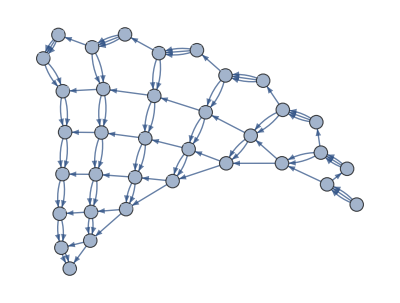
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss90=SSS[{"ABA"->"AAB","A"->"ABA"}, "A",75,SSSMax->25, NetMax->35,SSSSize->100,NetSize->400, VertexSize->0.6];
```

#### MaxStateLengthPositions: positions in "Evolution" where a new maximum state string length is reached for the first time

```mathematica
MaxStateLengthPositions[sss90]
```

{2,4,7,11,16,22,29,37,46,56}

Visually, these are the positions in the sessie (colored) image where the state string got longer.

```mathematica
CheckDimension@MaxStateLengthPositions[sss90]
```

{2D,{1,0,1},2
2
1,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Identified as (probably) 2-dimensional, pattern valid starting from position 2.  In the 0^th row, provided by MaxStateLengthPositions, we see rapid, increasing growth.  In the row of 1^st differences, growth is linear.  The 2^nd differences row is constant, and the 3^rd differences row would be all 0.  (This is reminiscent of taking derivatives of a quadratic (2^nd-degree) polynomial:  the first derivative is a linear function, the 2^nd is a constant, the 3^rd is zero.

#### LeastUsedRulePositions: positions where the least-used rule was used

```mathematica
LeastUsedRulePositions[sss90]
```

{1,3,6,10,15,21,28,36,45,55,66}

```mathematica
sss90["RulesUsed"]
```

{2,1,2,1,1,2,1,1,1,2,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1}

```mathematica
CheckDimension@LeastUsedRulePositions[sss90]
```

{2D,{1,0,1},1
2
1,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

Again, the 2nd differences row is constant, indicating 2-d behavior.

#### DistanceLastPositions: a list containing, for each positive integer n, the position of the last node that is n steps from origin on the undirected graph of "Net".

```mathematica
CheckDimension@DistanceLastPositions[sss90]
```

{2D,{1,0,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

#### DistanceTally: number of nodes in the undirected graph of "Net" that are no more than 1, 2, 3, ... steps from origin. (SSSAnimate[sss, VertexLabels → "VertexWeight"] gives a related, helpful visualization for the directed graph.)

```mathematica
CheckDimension@DistanceTally[sss90]
```

{2D,{1,3,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }

```mathematica
SSSAnimate[sss90,VertexLabels->"VertexWeight",NetSize->400]
```

#### GuessDimension: tries all 4 approximative tests, with appropriate checks, changes "Verdict" if appropriate.

```mathematica
GuessDimension[sss90]
```

{{2D,{1,0,1},2
2
1,2 | 4 | 7 | 11 | 16 | 22 | 29 | 37 | 46 | 56
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,1},1
2
1,1 | 3 | 6 | 10 | 15 | 21 | 28 | 36 | 45 | 55 | 66
2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,0,1},2
3
1,2 | 5 | 9 | 14 | 20 | 27 | 35 | 44 | 54 | 65
3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 |  | },{2D,{1,3,1},7
5
1,1 | 2 | 4 | 7 | 12 | 18 | 25 | 33 | 42 | 52 | 63
1 | 2 | 3 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 1 | 1 | 1 | 1 |  | }}

```mathematica
sss90["Verdict"]
```

2D

#### Other examples:

```mathematica
sss1a=SSS[{"A"->"",""->"A"},"",25,SSSSize->{50,200},NetSize->{400,300}, VertexSize->0.6];
sss1a["Verdict"]
```

```mathematica
CheckDimension@LeastUsedRulePositions[sss1a]
```

{1D,{1,0,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@MaxStateLengthPositions[sss1a]
```

{1D,{1,0,2},2
2,2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | }

```mathematica
CheckDimension@DistanceLastPositions[sss1a]
```

{failed,2
}

```mathematica
CheckDimension@DistanceTally[sss1a]
```

{failed,1
}

```mathematica
GuessDimension[sss1a]
```

Repeating

```mathematica
TestForUnusedRules[sss1a]
```

{}

If the sessie is disconnected, neither DistanceTally nor DistanceLastPositions may generate a usable list.  But fortunately, any repeating sessie can automatically be assumed to have dimension 1.   This is supported by all tests for repeating, connected cases.  So GuessDimension returns immediately in these cases.

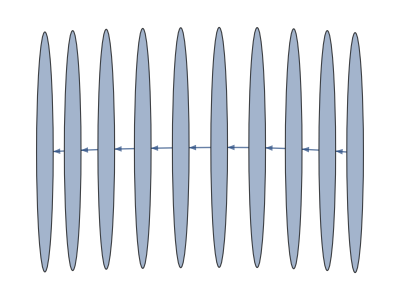
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

Repeating

Repeating

{}

```mathematica
sss1b=SSS[4,20,SSSSize->{50,200},Max->10,NetSize->{400,300}, VertexSize->0.6];
sss1b["Verdict"]
GuessDimension[sss1b]
TestForUnusedRules[sss1b]
```

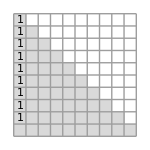
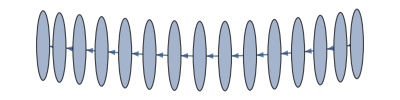
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

OK

{{1D,{1,0,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},2
1,2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | },{1D,{1,0,1},1
1,1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | }}

1D

{}

```mathematica
sss20=SSS[20,20,SSSMax->10,SSSSize->{150,150},NetMax->15,NetSize->{400,100}, VertexSize->.8];
sss20["Verdict"]
GuessDimension[sss20]
sss20["Verdict"]
TestForUnusedRules[sss20]
```

Note that GuessDimension has changed the "Verdict" field of sss20.

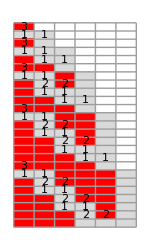



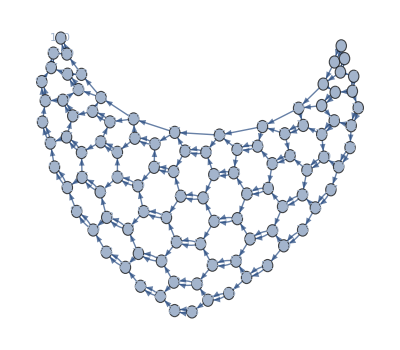
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

OK

{{2D,{1,0,2},7
5
2,7 | 12 | 19 | 28 | 39 | 52 | 67
5 | 7 | 9 | 11 | 13 | 15 | 
2 | 2 | 2 | 2 | 2 |  | },{2D,{1,0,2},6
5
2,6 | 11 | 18 | 27 | 38 | 51 | 66 | 83
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2D,{1,0,2},5
5
2,5 | 10 | 17 | 26 | 37 | 50 | 65 | 82
5 | 7 | 9 | 11 | 13 | 15 | 17 | 
2 | 2 | 2 | 2 | 2 | 2 |  | },{2D,{3,0,4/3},1 | 2 | 4
1 | 2 | 3
1 | 1 | 2,1 | 2 | 4 | 7 | 12 | 18 | 25 | 34 | 44 | 55
1 | 2 | 3 | 5 | 6 | 7 | 9 | 10 | 11 | 
1 | 1 | 2 | 1 | 1 | 2 | 1 | 1 |  | }}

2D

```mathematica
sssHex=SSS[{"AA"->"BA","AB"->"AA","B"->"AA"},"B",100,SSSMax->25,SSSSize->{150,250},NetMax->100,NetSize->{400,350}, VertexSize->1];
sssHex["Verdict"]
GuessDimension[sssHex]
sssHex["Verdict"]
```

```mathematica
TestForUnusedRules[sssHex]
```

{}

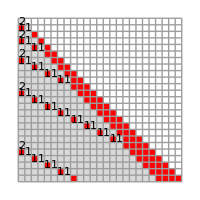
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

{{exp,{1,0,2},3
3
2,3 | 6 | 11 | 20 | 37 | 70 | 135 | 263
3 | 5 | 9 | 17 | 33 | 65 | 128 | 
2 | 4 | 8 | 16 | 32 | 63 |  | },{exp,{1,0,2},1
2
1,1 | 3 | 6 | 11 | 20 | 37 | 70 | 135 | 264
2 | 3 | 5 | 9 | 17 | 33 | 65 | 129 | 
1 | 2 | 4 | 8 | 16 | 32 | 64 |  | },{exp,{1,0,2},2
3
2,2 | 5 | 10 | 19 | 36 | 69 | 134
3 | 5 | 9 | 17 | 33 | 65 | 
2 | 4 | 8 | 16 | 32 |  | },{exp,{2,0,2},1 | 2
1 | 2
1 | 1,1 | 2 | 4 | 7 | 13 | 24 | 46 | 89
1 | 2 | 3 | 6 | 11 | 22 | 43 | 
1 | 1 | 3 | 5 | 11 | 21 |  | }}

exp

```mathematica
sssE=SSS[{"BA"->"AAB","A"->"BA"},"A",264,SSSMax->25,SSSSize->{200,200},NetSize->{400,300}, VertexLabels->None];
GuessDimension[sssE]
sssE["Verdict"]
```

```mathematica
TestForUnusedRules[sssE]
```

{}

If the sessie grows exponentially, growth positions are probably frequent and unimportant.  Only cross-checking with the rule used, done by the included MergeIntervalsByRulesUsed, permits limiting consideration to significant positions.

```mathematica
Length[sssE["Evolution"]]
```

265

CheckDimension identifies the network as exponential soon as the sequence of ratios appears.  FixedPointList would continue until lines have zero length:

```mathematica
FixedPointList[Differences,MaxStateLengthPositions[sssE]]//Column
```

{3,6,11,20,37,70,135,263}
{3,5,9,17,33,65,128}
{2,4,8,16,32,63}
{2,4,8,16,31}
{2,4,8,15}
{2,4,7}
{2,3}
{1}
{}
{}

Interestingly, here the exponential behavior was only found in the DistanceTally data when running averages of pairs of integers were summed, the raw data is harder to recognize:

```mathematica
FixedPointList[Differences,DistanceTally[sssE]]//Column
```

{1,2,4,7,13,24,46,89}
{1,2,3,6,11,22,43}
{1,1,3,5,11,21}
{0,2,2,6,10}
{2,0,4,4}
{-2,4,0}
{6,-4}
{-10}
{}
{}

```mathematica
MovingAverage[#,2]& /@ FixedPointList[Differences,DistanceTally[sssE]][[;;-4]]//Column
```

{3/2,3,11/2,10,37/2,35,135/2}
{3/2,5/2,9/2,17/2,33/2,65/2}
{1,2,4,8,16}
{1,2,4,8}
{1,2,4}
{1,2}
{1}

### Loop to display unique Sessies

<|Index→2,QCode→0,RuleSet→{A→,→A}|> : Repeating

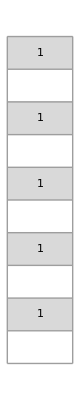
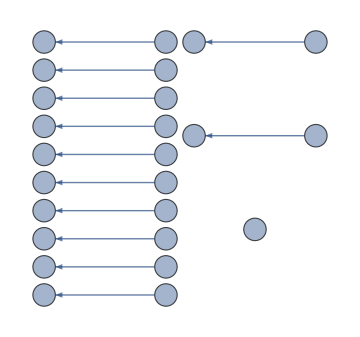
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→4,QCode→2,RuleSet→{A→A}|> : Repeating

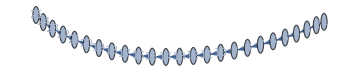
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→10,QCode→03,RuleSet→{A→,→AA}|> : Repeating

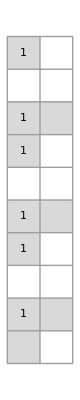
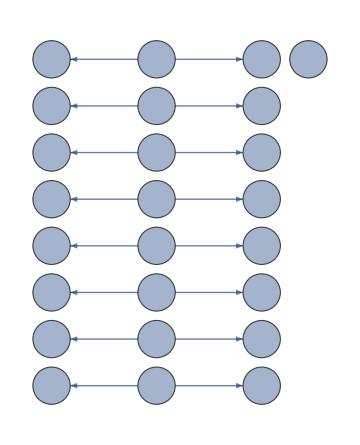
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→20,QCode→23,RuleSet→{A→AA}|> : 1D

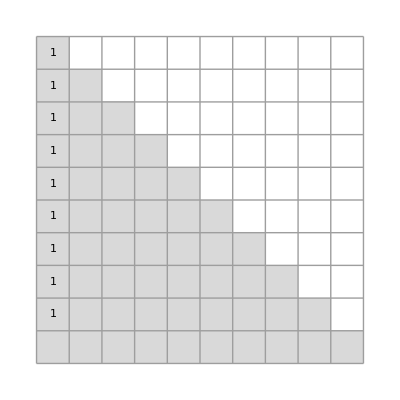
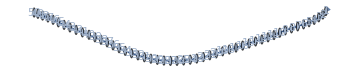
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→22,QCode→30,RuleSet→{AA→,→A}|> : Repeating

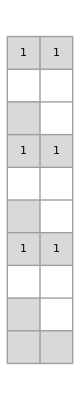
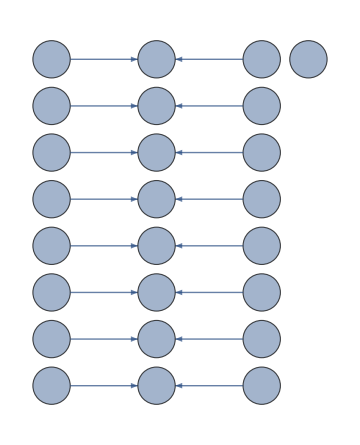
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→50,QCode→033,RuleSet→{A→,→AAA}|> : Repeating

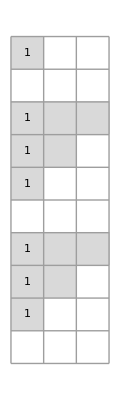
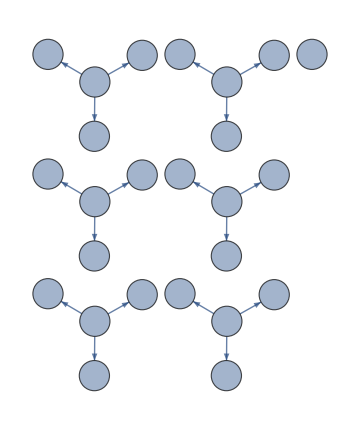
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→110,QCode→303,RuleSet→{AA→,→AA}|> : Repeating

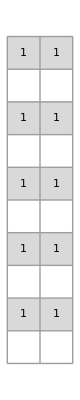
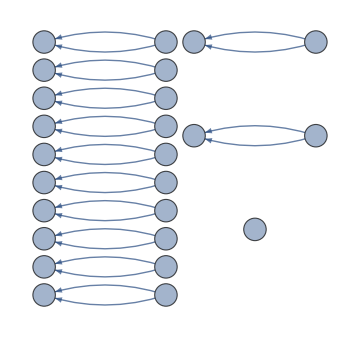
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→118,QCode→321,RuleSet→{AA→A,→A}|> : Repeating

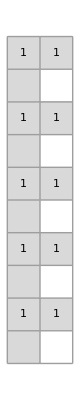
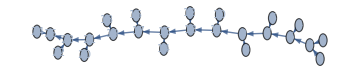
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→120,QCode→323,RuleSet→{AA→AA}|> : Repeating

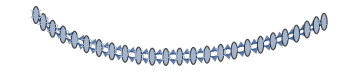
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→122,QCode→330,RuleSet→{AAA→,→A}|> : Repeating

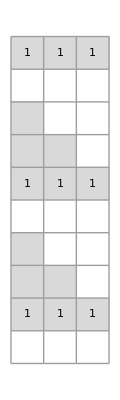
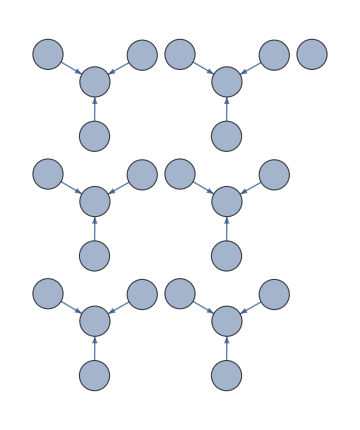
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {A→,→AAAA}: {}

<|Index→250,QCode→0333,RuleSet→{A→,→AAAA}|> : Repeating

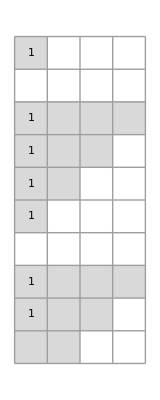
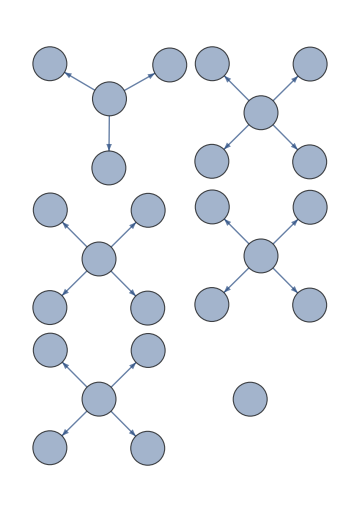
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→550,QCode→3033,RuleSet→{AA→,→AAA}|> : Repeating

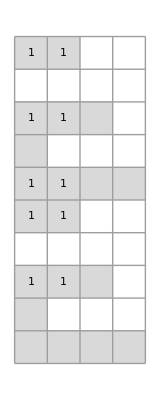
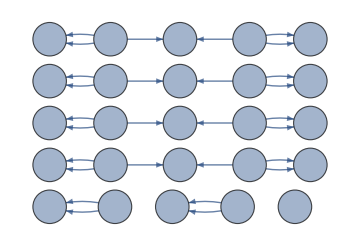
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→590,QCode→3213,RuleSet→{AA→A,→AA}|> : Repeating

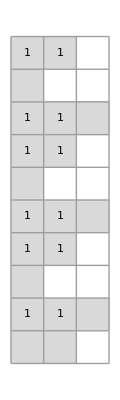
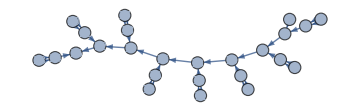
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→600,QCode→3233,RuleSet→{AA→AAA}|> : 1D

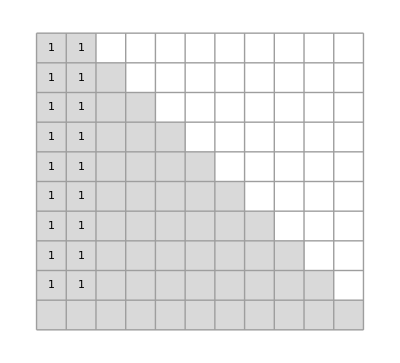
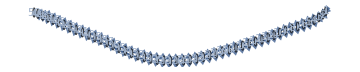
-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→610,QCode→3303,RuleSet→{AAA→,→AA}|> : Repeating

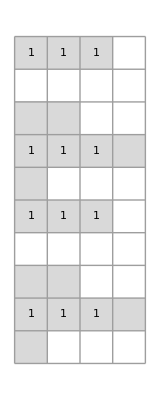
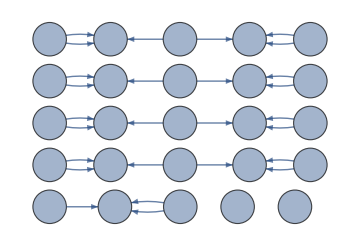
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→618,QCode→3321,RuleSet→{AAA→A,→A}|> : Repeating

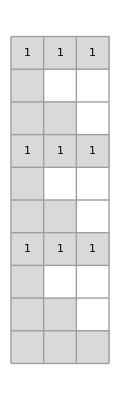
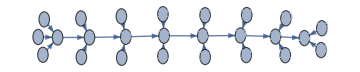
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {AAAA→,→A}: {}

<|Index→622,QCode→3330,RuleSet→{AAAA→,→A}|> : Repeating

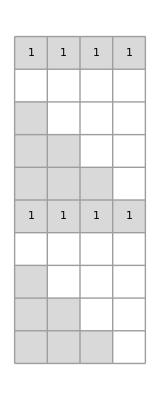
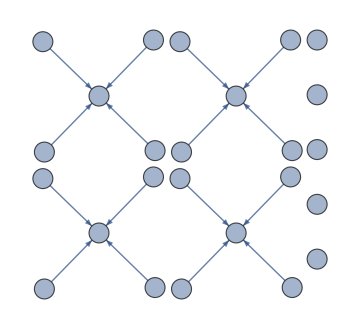
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {A→,→AAAAA}: {}

<|Index→1250,QCode→03333,RuleSet→{A→,→AAAAA}|> : Repeating

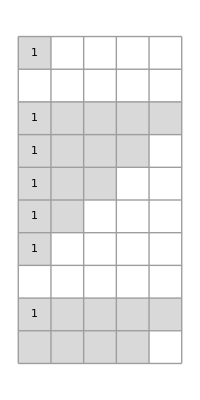
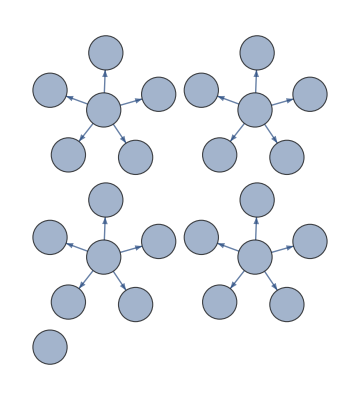
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1926,QCode→14034,RuleSet→{A→,B→,→AB}|> : Repeating

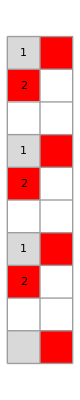
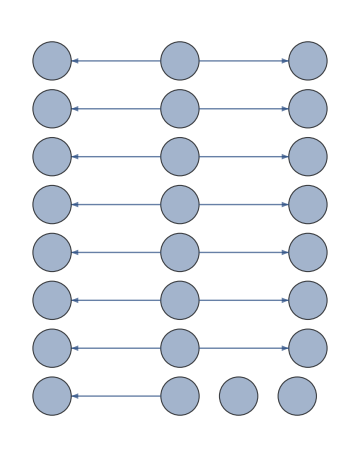
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1930,QCode→14043,RuleSet→{A→,B→,→BA}|> : Repeating

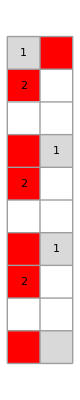
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1966,QCode→14214,RuleSet→{A→,B→A,→B}|> : Repeating

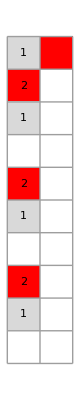
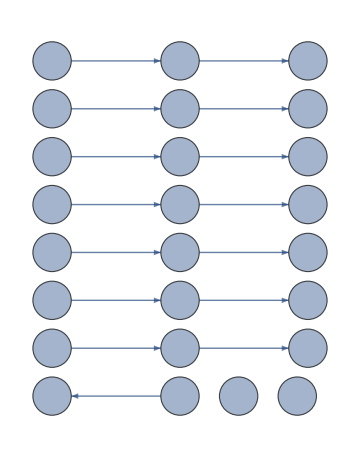
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1976,QCode→14234,RuleSet→{A→,B→AB}|> : Repeating

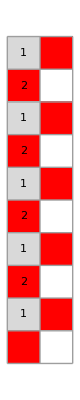
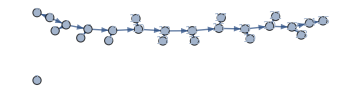
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→1980,QCode→14243,RuleSet→{A→,B→BA}|> : Repeating

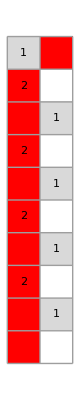
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2602,QCode→24240,RuleSet→{A→B,B→,→A}|> : Repeating

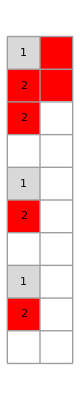
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2604,QCode→24242,RuleSet→{A→B,B→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2750,QCode→30333,RuleSet→{AA→,→AAAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2800,QCode→31033,RuleSet→{AA→,A→,→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2848,QCode→31231,RuleSet→{AA→,A→AA,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2950,QCode→32133,RuleSet→{AA→A,→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2960,QCode→32203,RuleSet→{AA→A,A→,→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→2970,QCode→32223,RuleSet→{AA→A,A→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3050,QCode→33033,RuleSet→{AAA→,→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3090,QCode→33213,RuleSet→{AAA→A,→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3098,QCode→33231,RuleSet→{AAA→AA,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3100,QCode→33233,RuleSet→{AAA→AAA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-Substitution Rule:-Graphics-

<|Index→3110,QCode→33303,RuleSet→{AAAA→,→AA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3118,QCode→33321,RuleSet→{AAAA→A,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

unreliable case: {AAAAA→,→A}: {}

<|Index→3122,QCode→33330,RuleSet→{AAAAA→,→A}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3176,QCode→34034,RuleSet→{AB→,→AB}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3180,QCode→34043,RuleSet→{AB→,→BA}|> : Repeating

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|> : OK

$Aborted

```mathematica
$debug=False;
rs=FromReducedRankIndex[1];               (* or other starting point in the enumeration *)
While[rs["Index"]<10^4,                         (* or some other large number, stopping point *)
(* Print[rs["Index"]]; *)
Which[
(Length[ans=TestForAll[rs]])>0,rs=ans; Continue[],  (* skip all possible *)

sss=SSS[rs["RuleSet"],25,Mode->Silent];  (* create the sessie for this ruleset *)
MatchQ[sss["Verdict"],"Dead"], (* do nothing! *) ,

GuessDimension[sss];
Length[ans=TestForUnusedRules[sss]]>0, rs=ans; Continue[], (* skip more! *)

True, (* else *)
Print[rs ," : ",sss⟦"Verdict"⟧];
Print@SSSDisplay[sss,SSSMax->10,SSSSize->Tiny,NetSize->Medium,VertexSize->0.8,VertexLabels->Placed[Automatic,Center]];
];
rs=FromReducedRankIndex[rs["Index"]+1]    (* increment *)
]
```

```mathematica
{rs,sss["Verdict"],Length[sss["Evolution"]],CheckDimension /@ {MaxStateLengthPositions[sss], LeastUsedRulePositions[sss],DistanceLastPositions[sss],DistanceTally[sss]}}
```

{<|Index→3216,QCode→34214,RuleSet→{AB→A,→B}|>,OK,12151,{{1D,{1,0,1},3
1,1},{1D,{1,0,1},2
1,1},{failed,
},{failed,
}}}
 |  |  |  |

```mathematica
$debug=False;
```

```mathematica
sssT=SSS[3216,25];
```

-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sssT["Verdict"]
```

OK

```mathematica
sssT["RulesUsed"]
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

```mathematica
TestForUnusedRules[sssT]
```

{}